```mathematica
<<Util`
```

```mathematica
<<PSD`
```

```mathematica
<<ErrorBarPlots`
```

```mathematica
<<PlotLegends`
```

```mathematica
ReadEventDat[fname_]:=Import[fname,"CSV"]
ReadEventMeta[fname_]:=Import[fname,"TSV"]⟦2;;⟧
ReadEventMetaColNames[fname_]:=Block[{tab},(tab[#⟦1⟧]=#⟦2⟧)&/@Transpose[{Import[fname,"TSV"]⟦1⟧,Range[Length[Import[datpath<>"/eventMD.tsv","TSV"]⟦1⟧]]}];
Return[tab]
]
DisplayEvents[eventMD_,eventTS_]:=
Manipulate[ListLinePlot[eventTS⟦i⟧,PlotRange->All,Epilog->{Black,Thick,Line[{{0,eventMD⟦i⟧⟦3⟧},{Length[eventTS⟦i⟧],eventMD⟦i⟧⟦3⟧}}],Line[{{0,eventMD⟦i⟧⟦2⟧},{Length[eventTS⟦i⟧],eventMD⟦i⟧⟦2⟧}}],Red,Line[{{eventMD⟦i⟧⟦4⟧,-400},{eventMD⟦i⟧⟦4⟧,400}}],Line[{{eventMD⟦i⟧⟦5⟧,-400},{eventMD⟦i⟧⟦5⟧,400}}]}],{i,1,Length[eventTS],1}]
```

```mathematica
Gauss1D[x_,α_,μ_,σ_]:=α Exp[-(x-μ)^2/(2 σ^2)]
```

```mathematica
ReadPyEventMeta[fname_]:=Block[{dat=Import[fname]⟦2;;⟧},
Return[Table[ToExpression[StringSplit[ToString[#],{"+/-"}]&/@dat⟦i⟧],{i,Length[dat]}]]
]
```

```mathematica
prange[dat_]:={All,0}/;Mean[dat]<0
prange[dat_]:={0,All}
```

```mathematica
evntplot[ts_,md_, txtpos_]:=ListLinePlot[ts⟦md⟦4⟧⟦1⟧-50;;md⟦5⟧⟦1⟧+50⟧,PlotRange->prange[ts],Frame->True,Epilog->{
Black,Thickness[Small],
 Line[{{0,md⟦2⟧⟦1⟧},{10000,md⟦2⟧⟦1⟧}}], Line[{{0,md⟦3⟧⟦1⟧},{10000,md⟦3⟧⟦1⟧}}], 
Red,Thickness[Small],
 Line[{{50-1,-500},{50-1,500}}],Line[{{50+(md⟦5⟧⟦1⟧-md⟦4⟧⟦1⟧)+1,-500},{50+(md⟦5⟧⟦1⟧-md⟦4⟧⟦1⟧)+1,500}}],
Blue,Text[Style[md⟦1⟧⟦1⟧,20],{50,txtpos}]
}]/;ToString[md⟦1⟧⟦1⟧]=="normal"
evntplot[ts_,md_, txtpos_]:=ListLinePlot[ts,PlotRange->prange[ts],Frame->True,PlotStyle->Gray,Epilog->{Red,Text[Style[md⟦1⟧⟦1⟧,20],{Length[ts]/2,txtpos}]}]
```

```mathematica
evnthist[ts_,md_]:=Show[{
ListPlot[PDF1D[Abs[ts],{0,Max[Abs[ts]]+20},1],PlotRange->All,PlotMarkers->Automatic,Frame->True,Epilog->{Black,Text[Style["o="<>ToString[md⟦2⟧⟦1⟧]<>"±"<>ToString[md⟦2⟧⟦2⟧]<>"\nb="<>ToString[md⟦3⟧⟦1⟧]<>"±"<>ToString[md⟦3⟧⟦2⟧],16],{70,0.02}]}],
Plot[Gauss1D[x,md⟦8⟧⟦2⟧,Abs[md⟦2⟧⟦1⟧],md⟦2⟧⟦2⟧]+Gauss1D[x,md⟦8⟧⟦1⟧,Abs[md⟦3⟧⟦1⟧],md⟦3⟧⟦2⟧],{x,0,150},PlotStyle->{Black,Thick}]
}]/;ToString[md⟦1⟧⟦1⟧]=="normal"
evnthist[ts_,md_]:=ListPlot[PDF1D[Abs[ts],{0,Max[Abs[ts]]+20},1],PlotRange->All,PlotMarkers->Automatic,PlotStyle->Gray,Frame->True]
```

```mathematica
pydispevent[ts_,md_,txtpos_:-30]:=Manipulate[
GraphicsRow[{
evntplot[ts⟦i⟧,md⟦i⟧,txtpos],
evnthist[ts⟦i⟧,md⟦i⟧]
}],{i,1,Length[ts],1}
]
```

```mathematica
ResTimeFit[dat_, rng_:{0.1,3.5}]:=Block[{a,b,t},Evaluate[Normal[NonlinearModelFit[PDF1D[Select[Flatten[ReadPyEventMeta[dat<>"/eventMD.tsv"]⟦All,7⟧],#≠-1&],rng,0.1],a Exp[-b t],{{a,.5},{b,2}},t]]]]
```

```mathematica
BlockDepthFit[dat_,rng_,δ_]:=Block[{a,b,c,x},
c/.FindFit[Hist1D[Select[ReadPyEventMeta[dat<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],rng,δ],a Exp[-(x-c)^2/(2 b^2)],{{a,100},{b,0.25},{c,0.25}},x]
]
```

```mathematica
PlotPEGBlockade[path_List,plotlabel_, rng_,binsz_]:=
ListLinePlot[Evaluate[Hist1D[Select[ReadPyEventMeta[#<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],rng,binsz]&/@path],PlotRange->All,PlotMarkers->None,PlotStyle->Thick,Frame->True,FrameTicksStyle->18,FrameLabel->{Style["Blockade Depth",18],Style["Counts",18]},Axes->False,PlotLabel->Style[plotlabel,20]]
```

```mathematica
MergePlotPEGBlockade[path_List,plotlabel_, rng_,binsz_]:=ListLinePlot[
Hist1D[Flatten[Select[ReadPyEventMeta[#<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&]&/@path],rng,binsz],PlotRange->All,PlotMarkers->None,PlotStyle->Thick,Frame->True,FrameTicksStyle->18,FrameLabel->{Style["Blockade Depth",18],Style["Counts",18]},Axes->False,PlotLabel->Style[plotlabel,20]]
```

```mathematica
PlotPEGData[path_List,plotlabel_, rng_,binsz_]:=
GraphicsRow[{
ListLinePlot[Evaluate[Hist1D[Select[ReadPyEventMeta[#<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],rng,binsz]&/@path],PlotRange->All,PlotMarkers->None,PlotStyle->Thick,Frame->True,FrameTicksStyle->18,FrameLabel->{Style["Blockade Depth",18],Style["Counts",18]},Axes->False],
Show[{
ListLogPlot[Evaluate[PDF1D[Select[Flatten[ReadPyEventMeta[#<>"/eventMD.tsv"]⟦All,7⟧],#≠-1&],{0.1,5},0.1]&/@path],PlotRange->All,Joined->False,PlotMarkers->{Automatic,14}],
LogPlot[Evaluate[ResTimeFit/@path],{t,0,5},PlotStyle->Thick]},Frame->True,FrameTicksStyle->18,FrameLabel->{Style["Res. Time (ms)",18],Style["Prob. Density (1/ms)",18]
}]
},PlotLabel->Style[plotlabel,20]]
```

datpath = "/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/SteadyStateHeating/20120725/21Cr1M40mV/"

```mathematica
ExpValue[pdf_]:=Total[(Times@@#)&/@pdf]/Total[pdf⟦All,2⟧]
```

### Misc

```mathematica
datpath="/Users/balijepalliak/Research/Experiments/PEGModelData/JoesData/"
```

/Users/balijepalliak/Research/Experiments/PEGModelData/JoesData/

```mathematica
ExtractBlockadeDepth[datpath_]:=Block[{s1=OpenRead[datpath<>"/eventProcessing.log"],ss},
ss=ToExpression[StringSplit[Last[StringSplit[Find[s1,"mdBlockDepth"]]],"+/-"]];
Close[s1];
Return[ss]
]
```

```mathematica
Reproducibility[bd_List]:={Mean[bd⟦All,1⟧],(√Total[bd⟦All,2⟧^2])/Length[bd]}
```

```mathematica
ErrorListPlot[{{#⟦1⟧,#⟦2⟧},ErrorBar[#⟦3⟧]}&/@Flatten/@Transpose[{
{40,60,80},(Reproducibility/@{
ExtractBlockadeDepth/@(datpath<>"m40mV/"<>#&/@{"P1","P2","P3"}),
ExtractBlockadeDepth/@(datpath<>"m60mV/"<>#&/@{"P1","P2","P3"}),
ExtractBlockadeDepth/@(datpath<>"m80mV/"<>#&/@{"P1","P2","P3"})
})
}],PlotRange->All,PlotMarkers->{Automatic,14},Frame->True,Axes->False,PlotStyle->Thick,FrameTicks->{{Automatic,None},{{40,60,80},None}},FrameTicksStyle->18,FrameLabel->{Style["V (mV)",18],Style["⟨i⟩/⟨i_0⟩",18]}]
```

-Graphics-

```mathematica
ErrorListPlot[{
{{40, Mean[ExtractBlockadeDepth/@(datpath<>"m40mV/"<>#&/@{"P1","P2","P3"})]},ErrorBar[StandardError[ExtractBlockadeDepth/@(datpath<>"m40mV/"<>#&/@{"P1","P2","P3"})]]},
{{60, Mean[ExtractBlockadeDepth/@(datpath<>"m60mV/"<>#&/@{"P1","P2","P3"})]},ErrorBar[StandardError[ExtractBlockadeDepth/@(datpath<>"m60mV/"<>#&/@{"P1","P2","P3"})]]},
{{80, Mean[ExtractBlockadeDepth/@(datpath<>"m80mV/"<>#&/@{"P1","P2","P3"})]},ErrorBar[StandardError[ExtractBlockadeDepth/@(datpath<>"m80mV/"<>#&/@{"P1","P2","P3"})]]}
},PlotRange->All,PlotMarkers->{Automatic,16},Frame->True,Axes->False,PlotStyle->Thick,FrameTicks->{{Automatic,None},{{40,60,80},None}},FrameTicksStyle->18,FrameLabel->{Style["V (mV)",18],Style["⟨i⟩/⟨i_0⟩",18]}]
```

-Graphics-

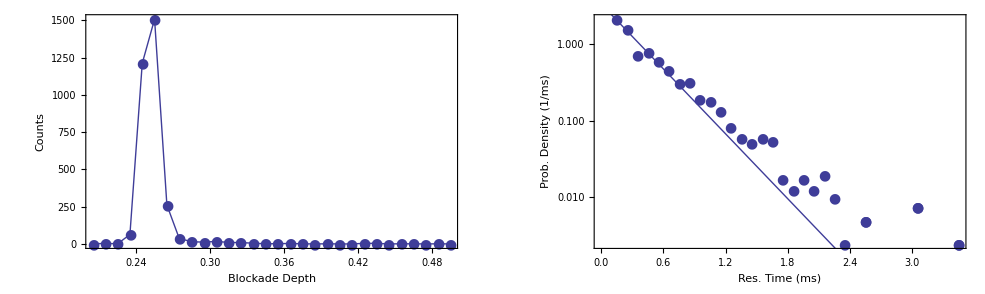

```mathematica
PlotPEGData[{datpath<>"/4M/60mV/"},""]
```

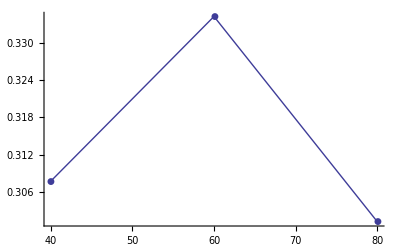

```mathematica
ListLinePlot[Transpose[{{40,60,80},N[ExtractBlockadeDepth/@{datpath<>"/4M/40mV/",datpath<>"/4M/60mV/",datpath<>"/4M/80mV/"}]⟦All,1⟧}],PlotRange->All, PlotMarkers->Automatic]
```

```mathematica
N[#[ExtractBlockadeDepth/@{(datpath<>"m40mV/"<>#&/@{"P1","P2","P3"})⟦2⟧,(datpath<>"m60mV/"<>#&/@{"P1","P2","P3"})⟦2⟧,(datpath<>"m80mV/"<>#&/@{"P1","P2","P3"})⟦2⟧}]&/@{Mean,StandardError}]
```

{0.315567,0.022165}

```mathematica
N[#[ExtractBlockadeDepth/@{Last[(datpath<>"m40mV/"<>#&/@{"P1","P2","P3"})],Last[(datpath<>"m60mV/"<>#&/@{"P1","P2","P3"})],Last[(datpath<>"m80mV/"<>#&/@{"P1","P2","P3"})]}]&/@{Mean,StandardError}]
```

{0.286567,0.00243059}

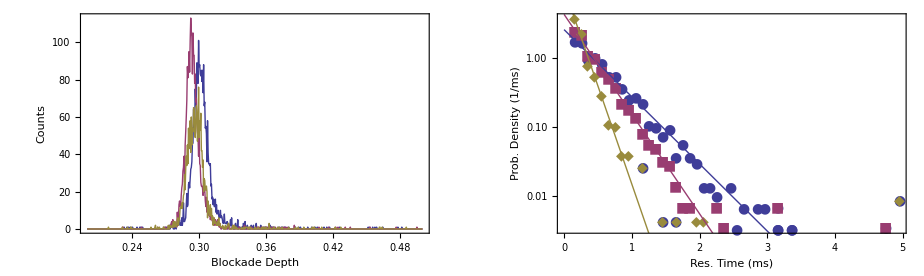

```mathematica
PlotPEGData[{datpath<>"3.5M/m40mV/p1",datpath<>"3.5M/m60mV/p1",datpath<>"3.5M/m80mV/p1"},"Pore 1",{0.2,0.5},0.0005]
```

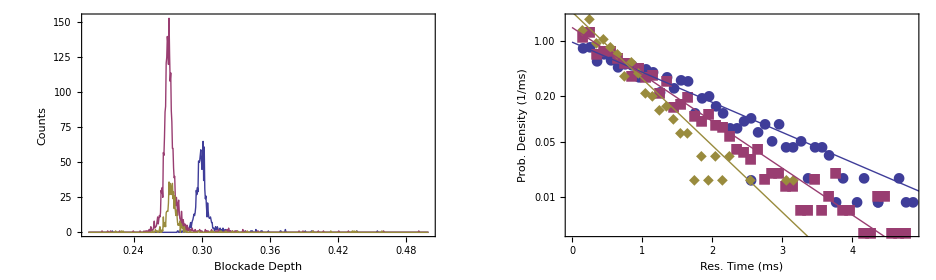

```mathematica
PlotPEGData[{datpath<>"3.5M/m40mV/p2",datpath<>"3.5M/m60mV/p2",datpath<>"3.5M/m80mV/p2"},"Pore 2",{0.2,0.5},0.0005]
```

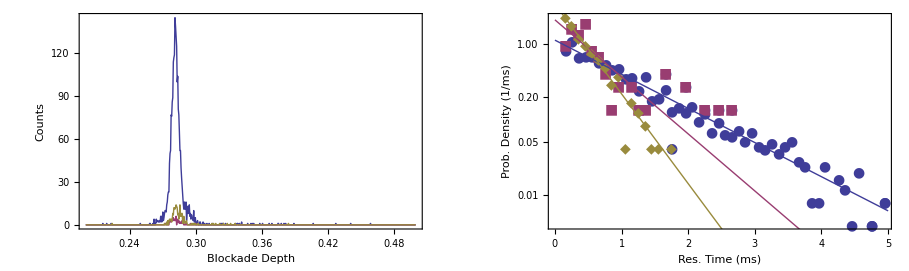

```mathematica
PlotPEGData[{datpath<>"3.5M/m40mV/p3",datpath<>"3.5M/m60mV/p3",datpath<>"3.5M/m80mV/p3"},"Pore 3",{0.2,0.5},0.0005]
```

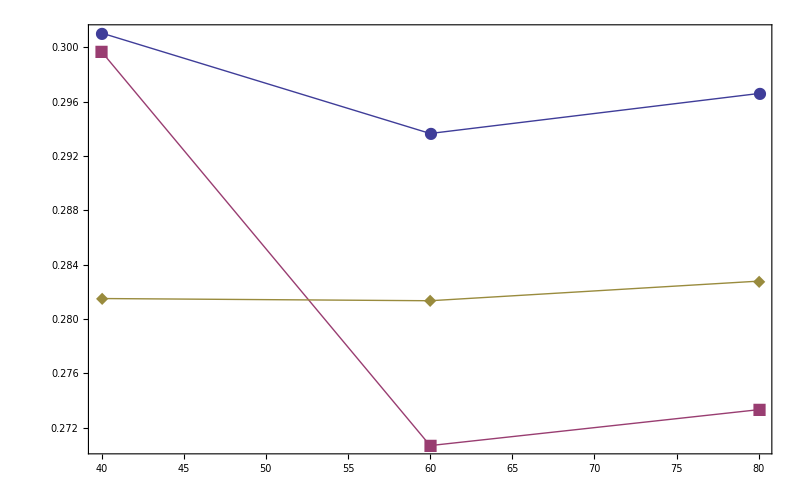

```mathematica
ListLinePlot[{
Transpose[{{40,60,80},BlockDepthFit[datpath<>#,{0.2,0.5},0.0005]&/@{"3.5M/m40mV/p1","3.5M/m60mV/p1","3.5M/m80mV/p1"}}],
Transpose[{{40,60,80},BlockDepthFit[datpath<>#,{0.2,0.5},0.0005]&/@{"3.5M/m40mV/p2","3.5M/m60mV/p2","3.5M/m80mV/p2"}}],
Transpose[{{40,60,80},BlockDepthFit[datpath<>#,{0.2,0.5},0.0005]&/@{"3.5M/m40mV/p3","3.5M/m60mV/p3","3.5M/m80mV/p3"}}]
},PlotRange->All,PlotMarkers->{Automatic,16},Frame->True,FrameTicksStyle->20]
```

```mathematica
TableForm[{
Mean[Select[ReadPyEventMeta[datpath<>"/"<>#<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&]]&/@{"2012_09_10_0000","2012_09_10_0010","2012_09_10_0016"},
{
1/b/.NonlinearModelFit[PDF1D[Select[Flatten[ReadPyEventMeta[datpath<>"/2012_09_10_0000/eventMD.tsv"]⟦All,7⟧],#≠-1&],{0.1,3.5},0.1],a Exp[-b t],{{a,.5},{b,2}},t]["BestFitParameters"],
1/b/.NonlinearModelFit[PDF1D[Select[Flatten[ReadPyEventMeta[datpath<>"/2012_09_10_0010/eventMD.tsv"]⟦All,7⟧],#≠-1&],{0.1,3.5},0.1],a Exp[-b t],{{a,.5},{b,2}},t]["BestFitParameters"],
1/b/.NonlinearModelFit[PDF1D[Select[Flatten[ReadPyEventMeta[datpath<>"/2012_09_10_0016/eventMD.tsv"]⟦All,7⟧],#≠-1&],{0.1,3.5},0.1],a Exp[-b t],{{a,.5},{b,2}},t]["BestFitParameters"]
}
},TableHeadings->{Style[#,16,FontFamily->"TimesNewRoman"]&/@{"Blockade Depth","Res. Time (ms)"},Style[#,16,FontFamily->"TimesNewRoman"]&/@{"Pore 1 (blue)","Pore 2 (purple)","Pore 3 (olive)"}}]
```

| Pore 1 (blue) | Pore 2 (purple) | Pore 3 (olive)
Blockade Depth | 0.314403 | 0.303708 | 0.290694
Res. Time (ms) | 0.447308 | 1.17707 | 0.96295

```mathematica
Evaluate[BlockDepthFit[datpath<>#,{0.2,0.35},0.0005]&/@{"/4M/40mV","/4M/60mV","/4M/80mV"}]
```

{0.250845,0.250865,0.252676}

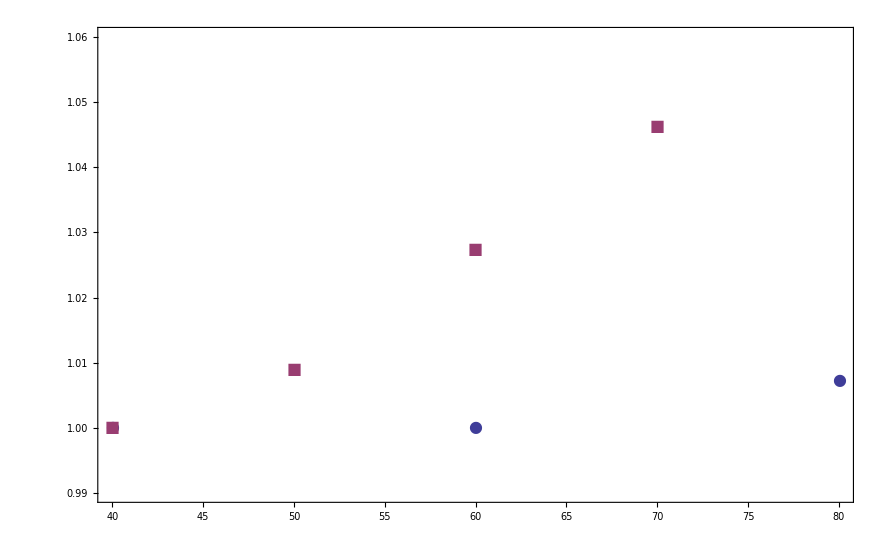

```mathematica
ListPlot[{
Transpose[{{40,60,80},1/0.250845 Evaluate[BlockDepthFit[datpath<>#,{0.2,0.35},0.0005]&/@{"/4M/40mV","/4M/60mV","/4M/80mV"}]}],Transpose[{{40,50,60,70},1/0.3482{ 0.3482,0.3513,0.3577,0.3643}}]

},PlotRange->{0.99,1.06},PlotMarkers->{Automatic,16},Frame->True,FrameTicksStyle->20]
```

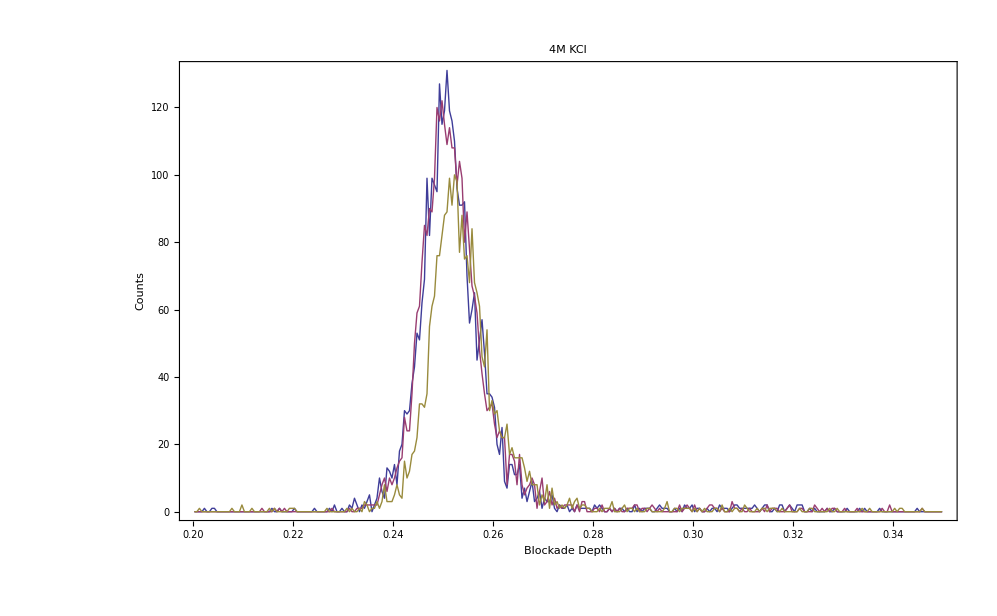

```mathematica
Show[{
PlotPEGBlockade[{datpath<>"/4M/40mV",datpath<>"/4M/60mV",datpath<>"/4M/80mV"},"4M KCl",{0.2,0.35},0.0005]
}]
```

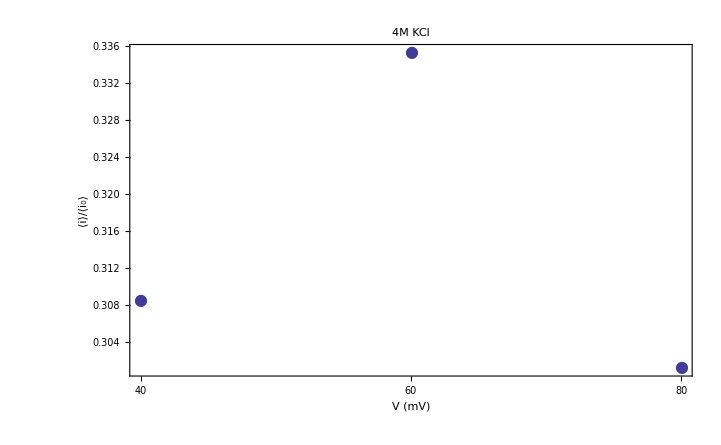

```mathematica
ErrorListPlot[{{#⟦1⟧,ExtractBlockadeDepth[datpath<>#⟦2⟧]⟦1⟧},ErrorBar[ExtractBlockadeDepth[datpath<>#⟦2⟧]⟦2⟧]}&/@{{40,"/4M/40mV"},{60,"/4M/60mV"},{80,"/4M/80mV"}},PlotRange->All,PlotMarkers->{Automatic,16},Frame->True,Axes->False,PlotStyle->Thick,FrameTicks->{{Automatic,None},{{40,60,80},None}},FrameTicksStyle->18,FrameLabel->{Style["V (mV)",18],Style["⟨i⟩/⟨i_0⟩",18]},PlotLabel->Style["4M KCl",20]]
```

```mathematica
WritePeakFinderFiles[datpath_,rng_,δ_]:=Block[{dd=Select[ReadPyEventMeta[datpath<>"/eventMD.tsv"], #⟦6⟧⟦1⟧≠-1&],h1},
h1=Hist1D[dd⟦All,6⟧⟦All,1⟧,rng,δ];
Return[{
Export[datpath<>"/bd_restime.tsv",Transpose[{dd⟦All,6⟧⟦All,1⟧,dd⟦All,2⟧⟦All,1⟧,dd⟦All,7⟧⟦All,1⟧,ConstantArray[0,Length[dd]]}],"TSV"],
Export[datpath<>"/bd_hist.tsv",h1,"TSV"]
}]
]
```

```mathematica
WritePeakFinderFiles[datpathJ<>"/7-6&7-2010_4M/"<>#,{0.1,0.4},0.00075]&/@{"40mV/","50mV/","60mV/","70mV/"}
```

{{/Users/balijepalliak/Research/Experiments/PEGModelData/JuliannesData//7-6&7-2010_4M/40mV//bd_restime.tsv,/Users/balijepalliak/Research/Experiments/PEGModelData/JuliannesData//7-6&7-2010_4M/40mV//bd_hist.tsv},{/Users/balijepalliak/Research/Experiments/PEGModelData/JuliannesData//7-6&7-2010_4M/50mV//bd_restime.tsv,/Users/balijepalliak/Research/Experiments/PEGModelData/JuliannesData//7-6&7-2010_4M/50mV//bd_hist.tsv},{/Users/balijepalliak/Research/Experiments/PEGModelData/JuliannesData//7-6&7-2010_4M/60mV//bd_restime.tsv,/Users/balijepalliak/Research/Experiments/PEGModelData/JuliannesData//7-6&7-2010_4M/60mV//bd_hist.tsv},{/Users/balijepalliak/Research/Experiments/PEGModelData/JuliannesData//7-6&7-2010_4M/70mV//bd_restime.tsv,/Users/balijepalliak/Research/Experiments/PEGModelData/JuliannesData//7-6&7-2010_4M/70mV//bd_hist.tsv}}

### Joe’s Data

```mathematica
datpath="/Users/balijepalliak/Research/Experiments/PEGModelData/JoesData/"
```

/Users/balijepalliak/Research/Experiments/PEGModelData/JoesData/

```mathematica
eem80=ReadPyEventMeta[datpath<>"/PEGMixture/3.5M_121712/m80mV/eventMD.tsv"];//AbsoluteTiming
```

{17.62388,Null}

```mathematica
eem60=ReadPyEventMeta[datpath<>"/PEGMixture/3.5M_121712/m60mV/eventMD.tsv"];//AbsoluteTiming
```

{18.74758,Null}

```mathematica
eem40 = ReadPyEventMeta[datpath <> "/PEGMixture/3.5M_121712/m40mV/eventMD.tsv"];//AbsoluteTiming
```

{9.46724,Null}

eem40 = ReadPyEventMeta[datpath <> "/PEGMixture/3.5M_1126/m40mV/eventMD.tsv"]; // AbsoluteTiming

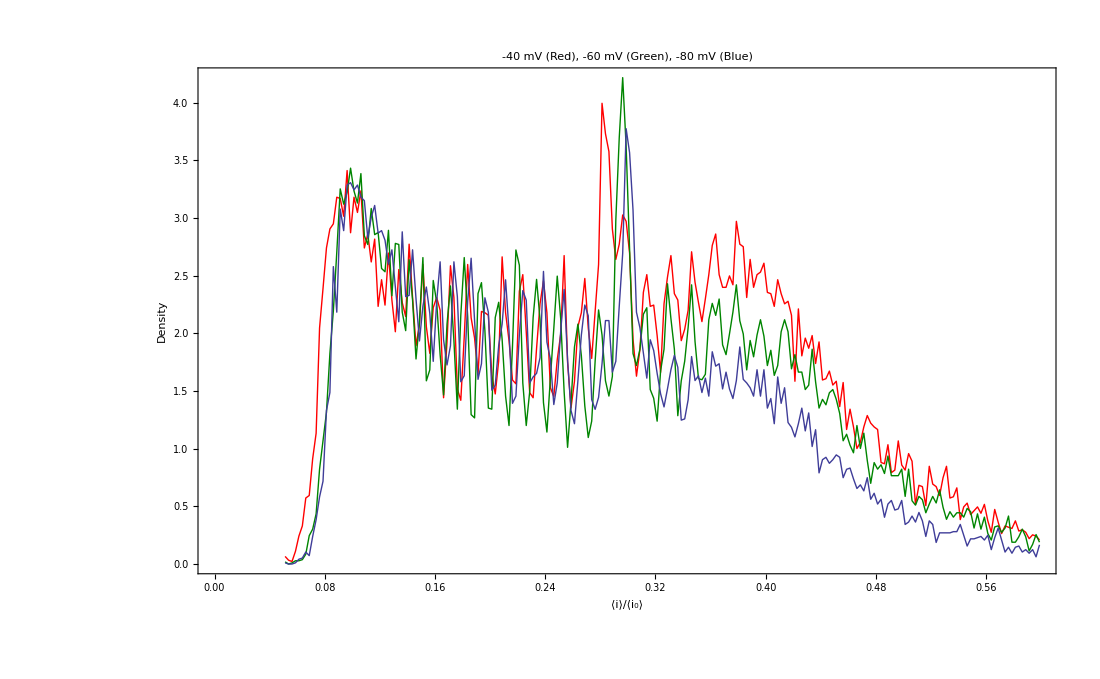

```mathematica
ListLinePlot[{
PDF1D[Select[eem40⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0025],
PDF1D[Select[eem60⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0025],
PDF1D[Select[eem80⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0025]
},PlotStyle->{Red,RGBColor[0,133/255,0],RGBColor[63/255,61/255,153/255]},PlotRange->{0,All},Frame->True,FrameTicksStyle->20,Axes->False,FrameLabel->{Style["⟨i⟩/⟨i_0⟩",20],Style["Density",20]},PlotLabel->Style["-40 mV (Red), -60 mV (Green), -80 mV (Blue)",20]]
```

```mathematica
eem40mV1212=ReadPyEventMeta[datpath<>"/PEGMixture/3.5M_121212/m40mV/eventMD.tsv"];//AbsoluteTiming
```

{8.66926,Null}

```mathematica
Export[HomeDirectory[]<>"/Desktop/hist.csv",Transpose[PadRight[PDF1D[Select[eem40mV1212⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0025]⟦All,2⟧,253,0]]]
```

/Users/balijepalliak/Desktop/hist.csv

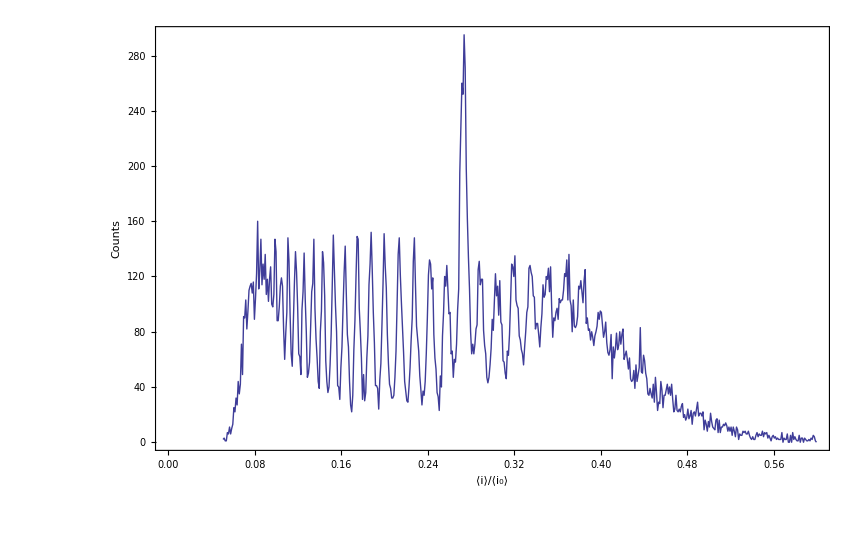

```mathematica
ListLinePlot[{
Hist1D[Select[eem40mV1212⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.001]
},PlotStyle->Thick,PlotRange->{0,All},Frame->True,FrameTicksStyle->20,Axes->False,FrameLabel->{Style["⟨i⟩/⟨i_0⟩",20],Style["Counts",20]}]
```

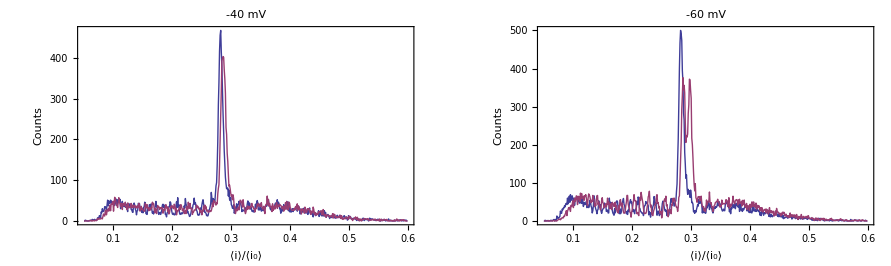

```mathematica
GraphicsRow[{
ListLinePlot[{
Hist1D[Select[eem40⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.001],
Hist1D[Select[eem40p2⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.001]
},PlotStyle->Thick,PlotRange->{0,All},Frame->True,FrameTicksStyle->20,Axes->False,FrameLabel->{Style["⟨i⟩/⟨i_0⟩",20],Style["Counts",20]},PlotLabel->Style["-40 mV",20]],
ListLinePlot[{
Hist1D[Select[ee⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.001],
Hist1D[Select[eem60p2⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.001]
},PlotStyle->Thick,PlotRange->{0,All},Frame->True,FrameTicksStyle->20,Axes->False,FrameLabel->{Style["⟨i⟩/⟨i_0⟩",20],Style["Counts",20]},PlotLabel->Style["-60 mV",20]]
}]
```

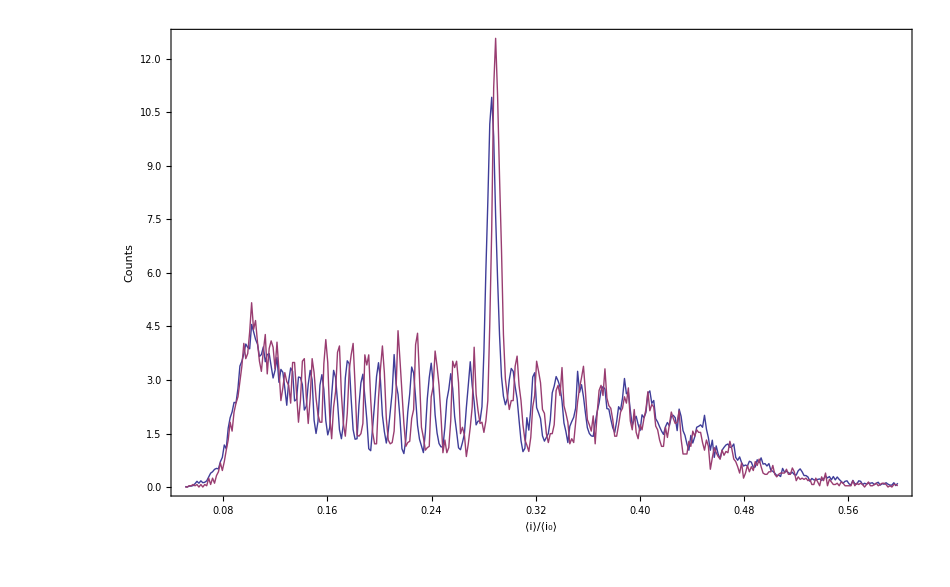

```mathematica
ListLinePlot[{
PDF1D[Select[eem40⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0015],
PDF1D[Select[ee⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0015]
},PlotStyle->Thick,PlotRange->{0,All},Frame->True,FrameTicksStyle->20,Axes->False,FrameLabel->{Style["⟨i⟩/⟨i_0⟩",20],Style["Counts",20]}]
```

```mathematica
1-CDF[NormalDistribution[0.19,0.09]][0.25+#]&/@{0.005,-0.005}
```

{0.235079,0.270563}

```mathematica
p1m40mV=Flatten[Select[ReadPyEventMeta[datpath<>"3.5M/m40mV/"<>#<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&]&/@{"p1","p2"}];
p1m60mV=Flatten[Select[ReadPyEventMeta[datpath<>"3.5M/m60mV/"<>#<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&]&/@{"p1","p3"}];
p1m80mV=Flatten[Select[ReadPyEventMeta[datpath<>"3.5M/m80mV/"<>#<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&]&/@{"p1","p3"}];
```

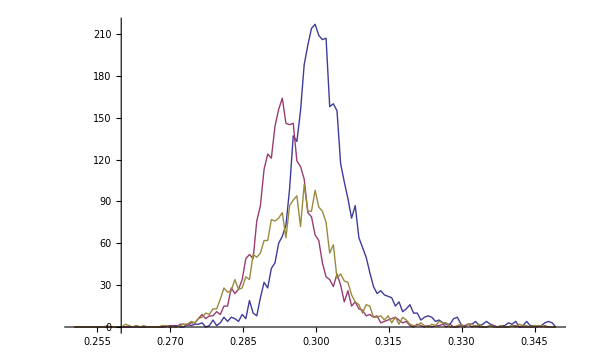

```mathematica
ListLinePlot[Evaluate[Hist1D[#,{0.25,0.35},0.00075]&/@{p1m40mV,p1m60mV,p1m80mV}],PlotRange->All]
```

```mathematica
ExpValue[Hist1D[#,{0.25,0.35},0.00075]]&/@{p1m40mV,p1m60mV,p1m80mV}
```

{0.301751,0.294488,0.295963}

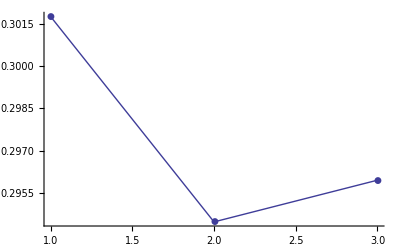

```mathematica
ListLinePlot[ExpValue[Hist1D[#,{0.25,0.35},0.00075]]&/@{p1m40mV,p1m60mV,p1m80mV},PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
p1m40mV4M=Select[ReadPyEventMeta[datpath<>"4M/40mV/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&];
p1m60mV4M=Select[ReadPyEventMeta[datpath<>"4M/60mV/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&];
p1m80mV4M=Select[ReadPyEventMeta[datpath<>"4M/80mV/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&];
```

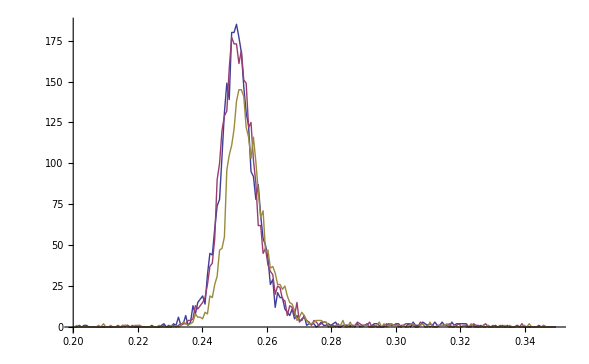

```mathematica
ListLinePlot[Evaluate[Hist1D[#,{0.2,0.35},0.00075]&/@{p1m40mV4M,p1m60mV4M,p1m80mV4M}],PlotRange->All]
```

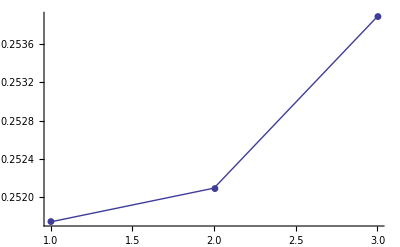

```mathematica
ListLinePlot[ExpValue[Hist1D[#,{0.2,0.3},0.00075]]&/@{p1m40mV4M,p1m60mV4M,p1m80mV4M},PlotRange->All,PlotMarkers->Automatic]
```

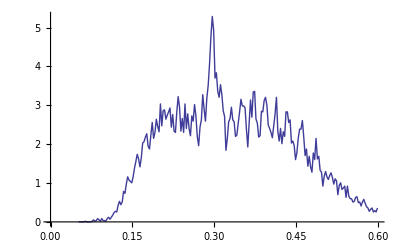

```mathematica
ListLinePlot[
PDF1D[Select[ReadPyEventMeta[datpath<>"/PEGMixture/3.44M_1413/m40mV_long/set1/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0025]]
```

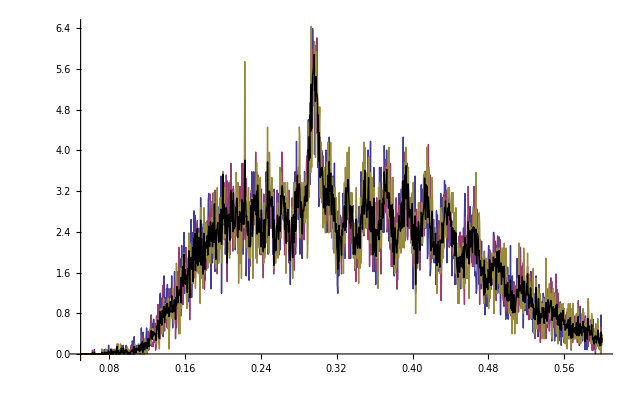

```mathematica
Show[{
ListLinePlot[{
PDF1D[Select[ReadPyEventMeta[datpath<>"/PEGMixture/3.44M_1413/m40mV_long/set1/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0005],
PDF1D[Select[ReadPyEventMeta[datpath<>"/PEGMixture/3.44M_1413/m40mV_long/set2/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0005],
PDF1D[Select[ReadPyEventMeta[datpath<>"/PEGMixture/3.44M_1413/m40mV_long/set3/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0005]
},PlotRange->All],
ListLinePlot[Mean[{
PDF1D[Select[ReadPyEventMeta[datpath<>"/PEGMixture/3.44M_1413/m40mV_long/set1/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0005],
PDF1D[Select[ReadPyEventMeta[datpath<>"/PEGMixture/3.44M_1413/m40mV_long/set2/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0005],
PDF1D[Select[ReadPyEventMeta[datpath<>"/PEGMixture/3.44M_1413/m40mV_long/set3/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.0005]
}],PlotRange->All,PlotStyle->{Black,Thick}]
}]
```

```mathematica
hist=Hist1D[Flatten[{
Select[ReadPyEventMeta[datpath<>"/PEGMixture/3.44M_1413/m40mV_long/set1/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],
Select[ReadPyEventMeta[datpath<>"/PEGMixture/3.44M_1413/m40mV_long/set2/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],
Select[ReadPyEventMeta[datpath<>"/PEGMixture/3.44M_1413/m40mV_long/set3/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&]
}],{0.05,0.6},0.001];
```

```mathematica
Export[HomeDirectory[]<>"/Desktop/tmp.csv",{PadRight[hist⟦All,2⟧,717]},"CSV"]
```

/Users/balijepalliak/Desktop/tmp.csv

```mathematica
"/Users/balijepalliak/Desktop/tmp.csv"
```

/Users/balijepalliak/Desktop/tmp.csv

```mathematica
peaks={36,88,110,121,138,154,169,184,198,213,246,281,300,321,343,364,387,413,439,467,496,532,543};
```

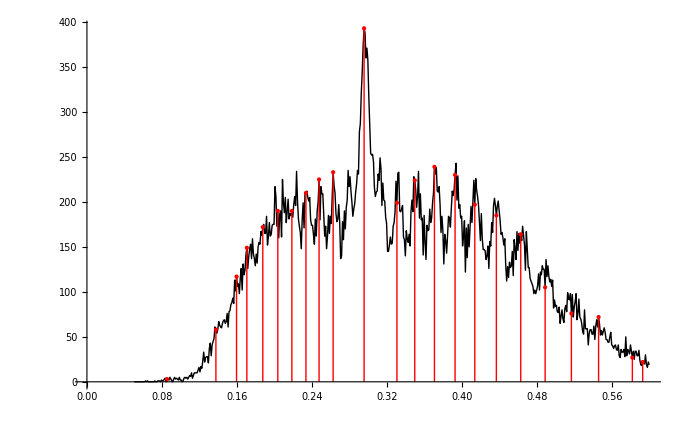

```mathematica
Show[{
ListLinePlot[hist,PlotStyle->{Black,Thick}],
ListPlot[hist⟦peaks⟧,PlotStyle->Red,Filling->Axis,FillingStyle->Red]
}]
```

### EBS AC Rig Data

```mathematica
dpath="/Users/balijepalliak/Research/Experiments/PEGModelData/ArvindsData/PEGMixture";
```

```mathematica
m60 = ReadPyEventMeta[dpath <> "/3M_20121219/m60mV12/eventMD.tsv"]; // AbsoluteTiming
```

```mathematica
m40 = Flatten[{
ReadPyEventMeta[dpath <> "/3M_20121219/m40mV13/eventMD.tsv"],
ReadPyEventMeta[dpath <> "/3M_20121219/m40mV12/eventMD.tsv"]
},1]; // AbsoluteTiming
```

{15.0481,Null}

```mathematica
m40⟦1000⟧
```

{{normal},{-129.695,1.4377},{-34.3403,1.2322},{74},{80},{0.26478,0.009944},{0.012},{0.160193,0.0488632}}

```mathematica
sm40=Select[m40,ToString[#⟦1⟧⟦1⟧]=="normal"&];
```

```mathematica
Manipulate[Graphics[{
Thick,
Line[{{sm40⟦i⟧⟦4⟧⟦1⟧-20,sm40⟦i⟧⟦2⟧⟦1⟧},{sm40⟦i⟧⟦4⟧⟦1⟧,sm40⟦i⟧⟦2⟧⟦1⟧}}],
Line[{{sm40⟦i⟧⟦5⟧⟦1⟧,sm40⟦i⟧⟦2⟧⟦1⟧},{sm40⟦i⟧⟦5⟧⟦1⟧+20,sm40⟦i⟧⟦2⟧⟦1⟧}}],
Line[{{sm40⟦i⟧⟦4⟧⟦1⟧,sm40⟦i⟧⟦3⟧⟦1⟧},{sm40⟦i⟧⟦5⟧⟦1⟧,sm40⟦i⟧⟦3⟧⟦1⟧}}],
Line[{{sm40⟦i⟧⟦4⟧⟦1⟧,sm40⟦i⟧⟦2⟧⟦1⟧},{sm40⟦i⟧⟦4⟧⟦1⟧,sm40⟦i⟧⟦3⟧⟦1⟧}}],
Line[{{sm40⟦i⟧⟦5⟧⟦1⟧,sm40⟦i⟧⟦2⟧⟦1⟧},{sm40⟦i⟧⟦5⟧⟦1⟧,sm40⟦i⟧⟦3⟧⟦1⟧}}]
},Axes->True,AxesOrigin->{0,-150},PlotRange->{{0,250},{0,-150}}],{i,1,Length[sm40],1}]
```

```mathematica
#[Select[Select[m40⟦All,2⟧⟦All,1⟧,#≠-1&],100<Abs[#]<200&]]&/@{Mean,StandardDeviation}
```

{-124.98,3.00888}

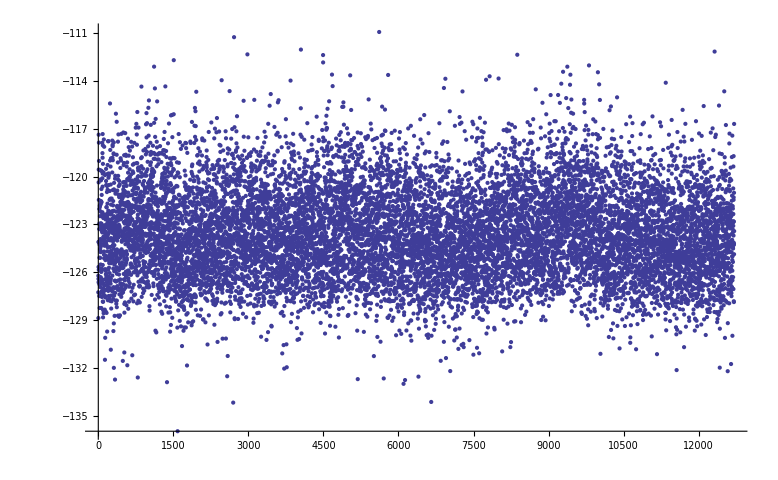

```mathematica
ListPlot[Select[Select[m40⟦All,2⟧⟦All,1⟧,#≠-1&],100<Abs[#]<200&],PlotRange->All]
```

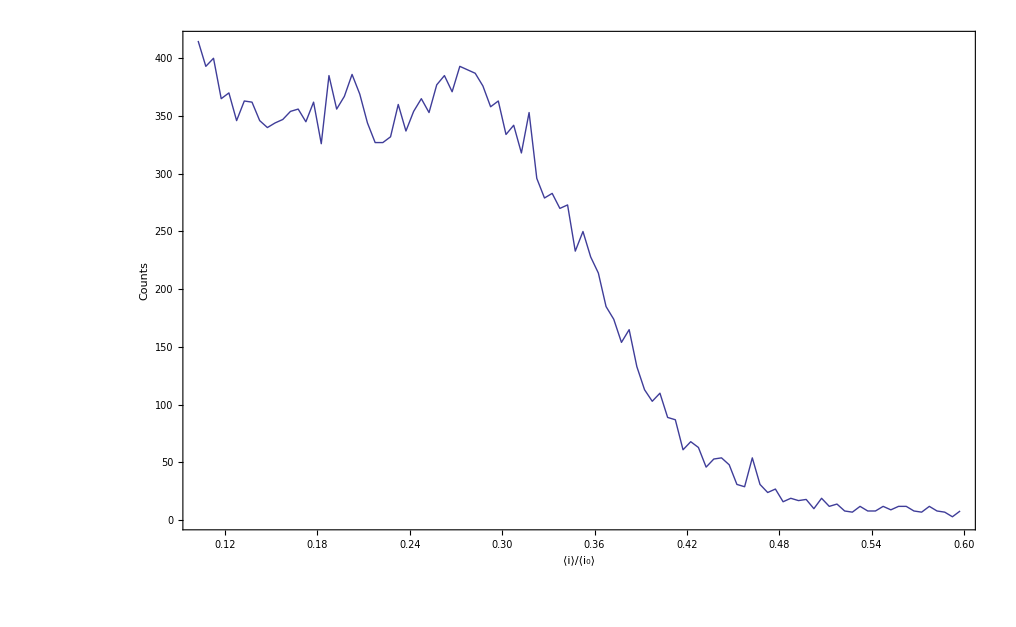

```mathematica
ListLinePlot[{
Hist1D[(#⟦2⟧/#⟦1⟧)&/@Select[Transpose[{Select[m40⟦All,2⟧⟦All,1⟧,#≠-1&],Select[m40⟦All,3⟧⟦All,1⟧,#≠-1&]}],100<Abs[#⟦1⟧]<200&],{0.1,0.6},0.005]
},PlotStyle->Thick,PlotRange->{0,All},Frame->True,FrameTicksStyle->20,Axes->False,FrameLabel->{Style["⟨i⟩/⟨i_0⟩",20],Style["Counts",20]}]
```

```mathematica
ReadEventMeta[dpath <> "/3M_20121219/m40mV13/eventMD.tsv"]⟦7⟧
```

{normal,-122.2416+/-5.6688,-40.4601+/-3.3945,73,171,0.33098+/-0.031728,0.196,0.0864221849732+/-0.00921764041336}

```mathematica
pydispevent[ReadEventDat[dpath <> "/3M_20121219/m40mV13/eventTS.csv"],ReadPyEventMeta[dpath <> "/3M_20121219/m40mV13/eventMD.tsv"]]
```

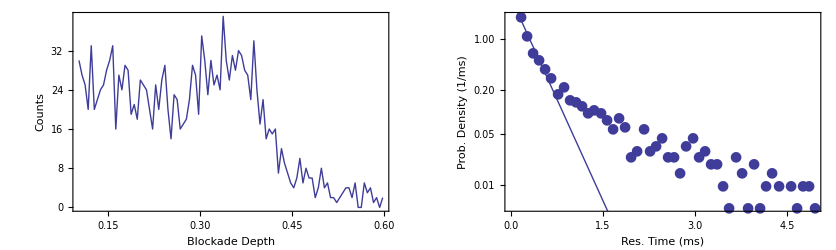

```mathematica
PlotPEGData[{dpath <> "/3M_20121219/m40mV13/"},"", {0.1,0.6},0.005]
```

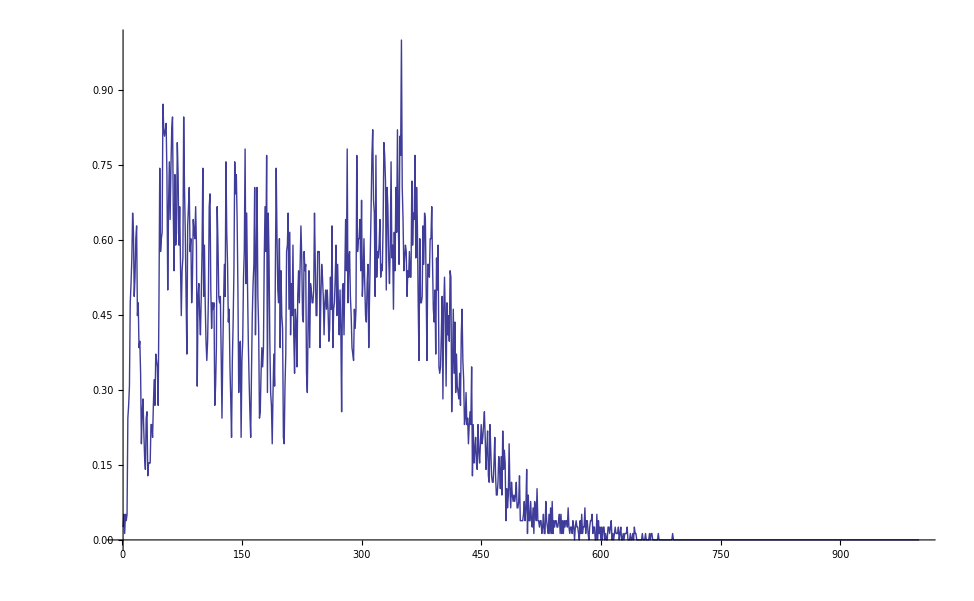

```mathematica
ListLinePlot[,PlotRange->All]
```

```mathematica
Export[HomeDirectory[]<>"/Desktop/hist.csv",Transpose[Flatten[Import[HomeDirectory[]<>"/Desktop/Rel_hist_comb.txt","CSV"]⟦2;;718⟧]]]
```

/Users/balijepalliak/Desktop/hist.csv

```mathematica
cwt=ContinuousWaveletTransform[Flatten[Import[HomeDirectory[]<>"/Desktop/Rel_hist_comb.txt","CSV"]⟦2;;⟧]]
```

ContinuousWaveletData[«CWT»,<8,4>,{999}]

```mathematica
{ws,oct,voc}=cwt[{"WaveletScale","Octaves","Voices"}]
```

{0.251646,8,4}

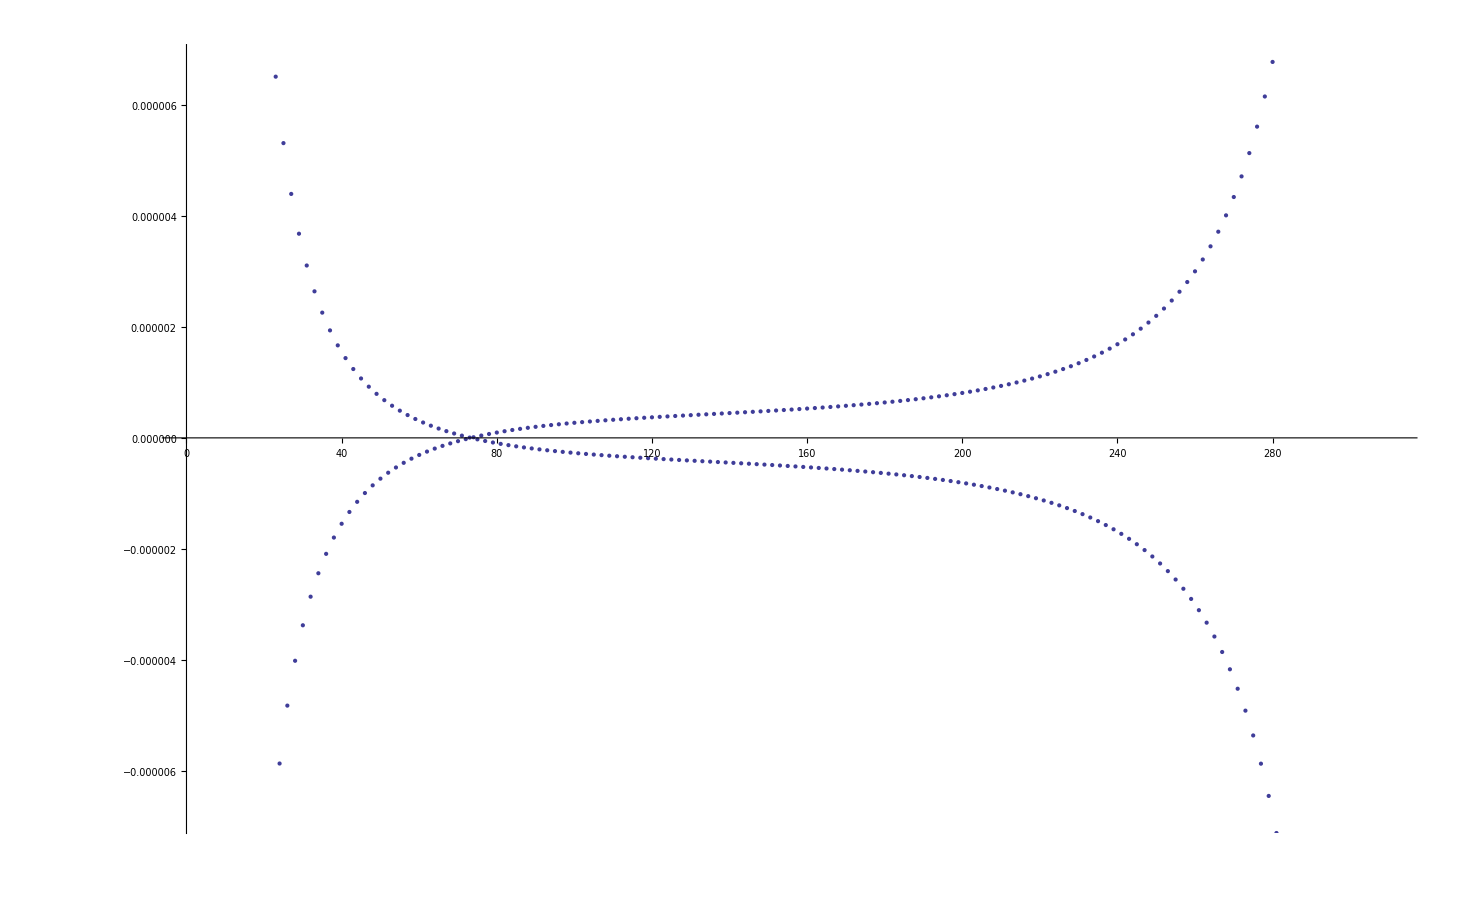

```mathematica
ListPlot[Select[({2,1}/.Normal[cwt]),Abs[#]<10^-4&]]
```

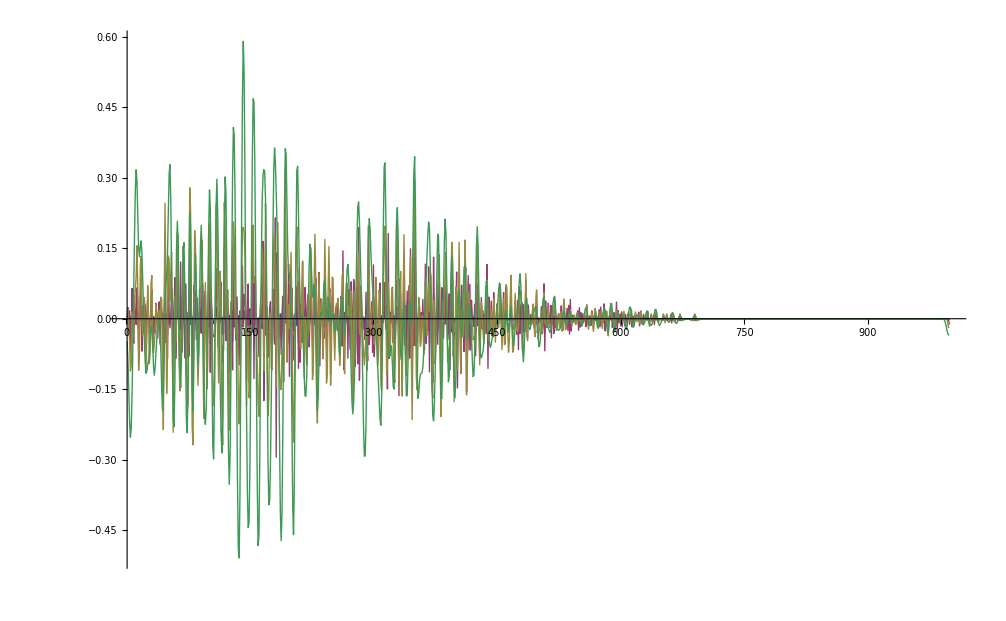

```mathematica
ListLinePlot[({#,1}/.Normal[cwt])&/@Range[4],PlotRange->All]
```

```mathematica
Mean[({#,1}/.Normal[cwt])&/@Range[2,5]]//Mean
```

3.51459×10^-18

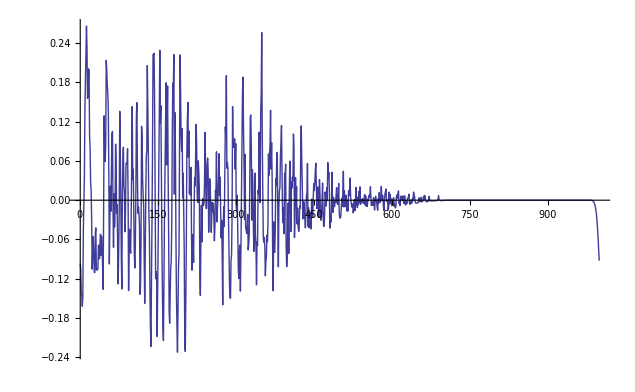

```mathematica
ListLinePlot[Mean[({#,1}/.Normal[cwt])&/@Range[5]],PlotRange->All]
```

```mathematica
WaveletScalogram[cwt,AxesLabel->{"time","scale"}]
```

-Graphics-

### τ error bars from peak finder output

```mathematica
GenErrBars[fname_]:=Block[{tt=ToExpression[Import[fname,"CSV"]],ft,dat,a,τ,t},
ft=Table[NonlinearModelFit[Transpose[Transpose[tt]⟦7+i;;7+i+1⟧]⟦2;;21⟧,a Exp[-t/τ],{{a,(Transpose[Transpose[tt]⟦7+i;;7+i+1⟧]⟦2;;21⟧)⟦1⟧⟦1⟧},{τ,tt⟦All,6⟧⟦IntegerPart[i/2]+2⟧}},t],{i,1,2  Length[tt⟦All,5⟧]-2,2}];
Partition[Flatten[{{"μ","SE","peak finder μ"},Flatten/@Transpose[{
#["ParameterTableEntries"]⟦2⟧⟦;;2⟧&/@ft,
tt⟦All,6⟧⟦2;;⟧
}]}],3]
]
```

```mathematica
PlotTauErrBars[file_]:=Block[{tt=ToExpression[Import[file,"CSV"]],a,t,τ},Manipulate[Block[{dat=Transpose[Transpose[tt]⟦7+i;;7+i+1⟧]⟦3;;21⟧,ft},
Show[{
ListLogPlot[dat,PlotRange->All,PlotMarkers->Automatic],
LogPlot[Evaluate[Normal[(ft=NonlinearModelFit[dat,a Exp[-t/τ],{{a,dat⟦1⟧⟦1⟧},{τ,tt⟦All,6⟧⟦IntegerPart[i/2]+2⟧}},t])]],{t,1,5000},PlotRange->All],
Graphics[Text[ft["ParameterTable"],Scaled[{0.75,0.75}]]]
}]
],{i,1,2  Length[tt⟦All,5⟧],2}]]
```

```mathematica
datpathA="/Users/balijepalliak/Research/Experiments/PEGModelData/ArvindsData/"
```

/Users/balijepalliak/Research/Experiments/PEGModelData/ArvindsData/

```mathematica
GenErrBars[datpathA<>"/PEGMixture/3M_20130116/pore8/reduced_m40mV8_6pts io1 analysis.csv"]
```

{{μ,SE,peak finder μ},{219.193,12.9259,382.467},{424.86,49.6139,533.309},{478.058,59.5357,656.99},{395.138,64.5195,542.999},{562.401,61.2415,652.31},{557.556,17.3416,591.366},{518.39,34.656,560.202},{588.093,46.7515,680.429},{405.167,18.214,444.114},{395.523,16.9389,418.935},{300.251,17.2983,317.693},{259.55,12.8558,278.675},{223.153,9.66322,230.546},{134.987,7.22033,150.746},{264.376,5.83877,268.605},{148.744,3.98547,154.028},{137.506,7.61275,140.182},{111.91,1.61108,112.982},{80.4991,4.31125,86.8844},{74.2121,1.72418,75.3634},{65.1078,1.40252,65.8158},{58.9729,2.34695,60.1995},{48.4035,0.824982,49.0231},{42.0788,1.22591,42.7558},{32.7869,0.643402,33.3004},{26.4358,1.20196,27.426},{20.8985,1.1586,22.0609},{13.0504,0.848762,14.8408},{6.11375,0.314912,7.24348}}

```mathematica
Export[datpathA<>"/PEGMixture/3M_20130116/pore8/tauerror_80mV.csv",GenErrBars[datpathA<>"/PEGMixture/3M_20130116/pore8/reduced_m80mV8_6pts io1 analysis.csv"],"CSV"]
```

/Users/balijepalliak/Research/Experiments/PEGModelData/ArvindsData//PEGMixture/3M_20130116/pore8/tauerror_80mV.csv

```mathematica
PlotTauErrBars[datpathA<>"/PEGMixture/4M_20130109/reducedoutput60mV1 io1 analysis output.csv"]
```

```mathematica
Dimensions[tt]
```

{28,62}

```mathematica
tt⟦All,5⟧⟦1+1⟧
```

652

```mathematica
(Differences/@Partition[Transpose[Transpose[tt]⟦7+1;;7+1+1⟧]⟦3;;21⟧⟦All,1⟧,2,1])0.02
```

{{4.467},{4.467},{4.467},{4.467},{4.467},{4.467},{4.467},{4.467},{4.467},{4.467},{4.467},{4.467},{4.467},{4.467},{4.467},{4.467},{4.467},{4.467}}

```mathematica
1/500000 1000//N
```

0.002

```mathematica
tt⟦All,6⟧⟦1+1⟧
```

1468.38

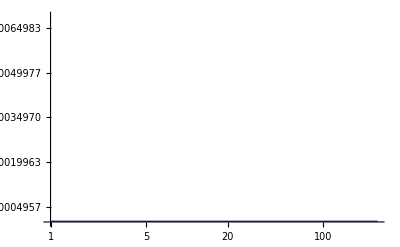

```mathematica
LogLinearPlot[Evaluate[a Exp[-t/τ]/.FindFit[Transpose[Transpose[tt]⟦7+1;;7+1+1⟧]⟦2;21⟧,a Exp[-t/τ],{a,{τ,tt⟦All,6⟧⟦1+1⟧}},t]],{t,1,250},PlotRange->All]
```

```mathematica
ft80=Table[NonlinearModelFit[Transpose[Transpose[tt]⟦7+i;;7+i+1⟧]⟦2;;21⟧,a Exp[-t/τ],{a,τ},t,MaxIterations->∞],{i,1,2  Length[tt⟦All,5⟧]-2,2}]
```

{FittedModel[324.755 ⅇ^(-0.123873 t)],FittedModel[83.379 ⅇ^(-0.00349563 t)],FittedModel[63.1017 ⅇ^(-0.00451208 t)],FittedModel[43.4557 ⅇ^(-0.00378952 t)],FittedModel[48.2701 ⅇ^(-0.00474672 t)],FittedModel[64.1974 ⅇ^(-0.00507921 t)],FittedModel[70.0195 ⅇ^(-0.00471369 t)],FittedModel[68.4632 ⅇ^(-0.00603746 t)],FittedModel[79.932 ⅇ^(-0.00673907 t)],FittedModel[65.3847 ⅇ^(-0.00548741 t)],FittedModel[94.7897 ⅇ^(-0.00789693 t)],FittedModel[77.4342 ⅇ^(-0.00658932 t)],FittedModel[84.6119 ⅇ^(-0.0073429 t)],FittedModel[83.7089 ⅇ^(-0.00824432 t)],FittedModel[144.82 ⅇ^(-0.0106302 t)],FittedModel[131.094 ⅇ^(-0.0116318 t)],FittedModel[146.455 ⅇ^(-0.0138047 t)],FittedModel[167.081 ⅇ^(-0.014508 t)],FittedModel[158.508 ⅇ^(-0.017935 t)],FittedModel[355.652 ⅇ^(-0.0198817 t)],FittedModel[269.936 ⅇ^(-0.0297517 t)],FittedModel[291.536 ⅇ^(-0.0316396 t)],FittedModel[251.42 ⅇ^(-0.0371404 t)],FittedModel[429.75 ⅇ^(-0.0459162 t)],FittedModel[451.859 ⅇ^(-0.0585254 t)],FittedModel[387.85 ⅇ^(-0.0791817 t)],FittedModel[465.275 ⅇ^(-0.101638 t)],FittedModel[564.989 ⅇ^(-0.117164 t)],FittedModel[677.674 ⅇ^(-0.137515 t)],FittedModel[1356.44 ⅇ^(-0.214245 t)],FittedModel[2418. ⅇ^(-0.313881 t)],FittedModel[1187.63 ⅇ^(-0.272959 t)],FittedModel[40232.6 ⅇ^(-0.758542 t)],FittedModel[1.05707×10^16 ⅇ^(-4.44082 t)],FittedModel[7.86144×10^128 ⅇ^(-40.8342 t)]}

```mathematica
Partition[Flatten[{{"μ","SE","peak finder μ"},Flatten/@Transpose[{
#["ParameterTableEntries"]⟦2⟧⟦;;2⟧&/@ft80,
tt⟦All,6⟧⟦2;;⟧
}]}],3]
```

{{μ,SE,peak finder μ},{8.07275,392802.,302.027},{286.071,20.4804,306.144},{221.627,12.8727,233.649},{263.885,20.211,309.674},{210.672,16.8836,243.386},{196.881,14.7567,212.481},{212.148,14.7193,239.196},{165.633,11.1894,180.197},{148.389,17.9652,164.86},{182.235,12.3817,196.154},{126.631,12.6947,142.147},{151.761,12.9726,160.526},{136.186,6.56341,143.517},{121.296,7.92248,128.376},{94.0712,5.13845,102.71},{85.9709,7.55679,87.5382},{72.4389,5.51321,78.9195},{68.9277,3.66627,70.6087},{55.757,3.98981,62.3737},{50.2974,2.71869,50.3516},{33.6116,1.577,35.3101},{31.606,0.894849,32.5938},{26.9249,1.43527,28.1625},{21.7788,0.886343,22.5023},{17.0866,0.650598,17.4136},{12.6292,0.840813,13.1618},{9.83881,0.831056,10.6271},{8.53503,0.580678,9.34012},{7.27195,0.287282,7.66057},{4.66754,0.537282,5.72797},{3.18592,0.381582,4.01414},{3.66356,0.163367,3.76716},{1.31832,0.318128,2.69055},{0.225184,0.00111432,1.91312},{0.0244893,0.0000161122,1.89923}}

```mathematica
tt⟦All,6⟧⟦2;;⟧//Length
```

40

40

```mathematica
Manipulate[
Show[{
ListLogLinearPlot[Transpose[Transpose[tt]⟦7+i;;7+i+1⟧]⟦2;;21⟧,PlotRange->All,PlotMarkers->Automatic],
LogLinearPlot[Evaluate[a Exp[-t/τ]/.FindFit[Transpose[Transpose[tt]⟦7+i;;7+i+1⟧]⟦2;;21⟧,a Exp[-t/τ],{a,{τ,tt⟦All,6⟧⟦i+1⟧}},t]],{t,1,250}]
}],{i,1,2 Length[tt⟦All,5⟧]-1,2}]
```

### τ error bars part deux

```mathematica
TrWith[dat_,lvl_]:=Transpose[{dat,lvl&/@Range[Length[dat]]}]
```

```mathematica
bdPeaks1[eventdat_, n_] := #[Mean /@ Partition[eventdat[[All, 2]], IntegerPart[Length[eventdat]/n]]] & /@ {Mean, StandardError}
```

```mathematica
bdPeaks[eventdat_, n_,binSz_]:=Block[{dat=Partition[eventdat⟦All,2⟧,IntegerPart[Length[eventdat]/n]],a,μ,σ,x,tt,hh,μe,ae,σe,i},

hh=Hist1D[#,{Min[#]-2×binSz,Max[#]+2×binSz},binSz]&/@dat;
{μe,σe,ae}={Mean[eventdat⟦All,2⟧],StandardDeviation[eventdat⟦All,2⟧],Length[eventdat⟦All,2⟧]};
tt=Table[μ/.FindFit[hh⟦i⟧, a Exp[-(x-μ)^2/(2 σ^2)],{{a,ae},{μ,μe},{σ,σe}},x,MaxIterations->5000],{i,Length[hh]}];
Return[{Mean[tt],StandardError[tt]}];
]
```

```mathematica
τPeaks[eventdat_,n_ , binSz_,FsKHz_]:=Block[{ττ=Partition[eventdat⟦All,3⟧,IntegerPart[Length[eventdat]/n]],hh,τ,a,t,restime},
hh=Hist1D[#,{Min[#]-2×binSz,Max[#]+2×binSz},binSz]&/@ττ;
restime=Table[τ/.NonlinearModelFit[hh⟦i⟧,a Exp[-t/τ],{{a, Max[hh⟦i⟧⟦All,2⟧]},{τ,Mean[ττ⟦i⟧]}},t,MaxIterations->∞]["BestFitParameters"],{i,Length[hh]}];
Return[{Mean[restime],StandardError[restime]}/FsKHz]
]
```

```mathematica
nPeaks[eventdat_]:=Length[eventdat]
```

```mathematica
JoesModifiedPeakFinder[datpath_, prefix_,stdn_]:=Block[{peak,bd, res, sop,tt},
peak=Flatten[{
IntegerPart/@ToExpression[StringSplit[Import[datpath<>prefix<>"_peaknumber1","Text"]]],IntegerPart/@ToExpression[StringSplit[Import[datpath<>prefix<>"_peaknumber2","Text"]]]}];
bd=ToExpression[StringSplit[Import[datpath<>prefix<>"_blockdepth","Text"]]]⟦;;Length[peak]⟧;
res=ToExpression[StringSplit[Import[datpath<>prefix<>"_restimes","Text"]]]⟦;;Length[peak]⟧;
sop=GatherBy[SortBy[Transpose[{peak,bd,res}],First], First];

tt=Flatten/@Transpose[{bdPeaks[#,3,0.001]&/@sop,nPeaks/@sop,τPeaks[#,3,25,500]&/@sop,bdPeaks1[#,3]&/@sop}];

Return[AlignPeaksToPolymerN[#⟦;;3⟧&/@tt,Flatten[{#⟦4;;5⟧,#⟦4⟧}]&/@tt,stdn]]
]
```

```mathematica
JoesModifiedPeakFinder[datpath_, prefix_]:=Block[{peak,bd, res, sop,tt},
peak=Flatten[{
IntegerPart/@ToExpression[StringSplit[Import[datpath<>prefix<>"_peaknumber1","Text"]]],IntegerPart/@ToExpression[StringSplit[Import[datpath<>prefix<>"_peaknumber2","Text"]]]}];
bd=ToExpression[StringSplit[Import[datpath<>prefix<>"_blockdepth","Text"]]]⟦;;Length[peak]⟧;
res=ToExpression[StringSplit[Import[datpath<>prefix<>"_restimes","Text"]]]⟦;;Length[peak]⟧;
sop=GatherBy[SortBy[Transpose[{peak,bd,res}],First], First];

tt=Flatten/@Transpose[{bdPeaks[#,3,0.001]&/@sop,nPeaks/@sop,τPeaks[#,3,25,500]&/@sop,bdPeaks1[#,3]&/@sop}];

Return[tt]
]
```

```mathematica
(tt=JoesModifiedPeakFinder["/Users/balijepalliak/Research/Experiments/PEGModelData/ArvindsData/PEGMixture/200us rejection/3.5M_20130211/test/","m40mV_3p5M_50pts io1 analysis output",29])//TableForm
```

42 | 0.147695 | 0.000927402 | 90 | 3.10625 | 0.743359
41 | 0.154169 | 0.000944485 | 127 | 2.35701 | 0.867511
40 | 0.162322 | 0.00117923 | 205 | 1.9791 | 0.492622
39 | 0.170471 | 0.000960342 | 246 | 2.29093 | 0.722501
38 | 0.180012 | 0.00125422 | 390 | 1.77648 | 0.276265
37 | 0.189883 | 0.00119263 | 419 | 1.84158 | 0.44801
36 | 0.200854 | 0.00133668 | 513 | 1.69213 | 0.369322
35 | 0.212686 | 0.00139657 | 642 | 1.44597 | 0.30158
34 | 0.224851 | 0.00147767 | 699 | 1.42648 | 0.345013
33 | 0.237787 | 0.00168817 | 863 | 1.22255 | 0.244234
32 | 0.251448 | 0.00154535 | 843 | 1.16304 | 0.230261
31 | 0.265732 | 0.00181833 | 930 | 0.986765 | 0.175272
30 | 0.280512 | 0.00182129 | 981 | 0.867565 | 0.118374
29 | 0.295317 | 0.00179552 | 1607 | 0.814413 | 0.111718
28 | 0.311036 | 0.00196189 | 1102 | 0.737852 | 0.103762
27 | 0.327056 | 0.00227169 | 1036 | 0.646416 | 0.0840706
26 | 0.343018 | 0.00223844 | 1143 | 0.597547 | 0.0661295
25 | 0.359507 | 0.00225862 | 1206 | 0.524245 | 0.0441378
24 | 0.381135 | 0.00317183 | 1241 | 0.516436 | 0.0476479
23 | 0.393352 | 0.00266182 | 1257 | 0.474077 | 0.0248535
22 | 0.411166 | 0.00270382 | 1240 | 0.445623 | 0.017601
21 | 0.429418 | 0.00306366 | 1036 | 0.43121 | 0.0425342
20 | 0.449191 | 0.00311588 | 885 | 0.384661 | 0.0121257
19 | 0.469869 | 0.00313915 | 617 | 0.399233 | 0.0474848
18 | 0.492486 | 0.00386913 | 434 | 0.443482 | 0.064685
17 | 0.52361 | 0.00548249 | 393 | 0.547448 | 0.0584042

```mathematica
//TableForm
```

42 | 0.147695 | 0.000927402 | 90 | 3.10625 | 0.743359
41 | 0.154169 | 0.000944485 | 127 | 2.35701 | 0.867511
40 | 0.162322 | 0.00117923 | 205 | 1.9791 | 0.492622
39 | 0.170471 | 0.000960342 | 246 | 2.29093 | 0.722501
38 | 0.180012 | 0.00125422 | 390 | 1.77648 | 0.276265
37 | 0.189883 | 0.00119263 | 419 | 1.84158 | 0.44801
36 | 0.200854 | 0.00133668 | 513 | 1.69213 | 0.369322
35 | 0.212686 | 0.00139657 | 642 | 1.44597 | 0.30158
34 | 0.224851 | 0.00147767 | 699 | 1.42648 | 0.345013
33 | 0.237787 | 0.00168817 | 863 | 1.22255 | 0.244234
32 | 0.251448 | 0.00154535 | 843 | 1.16304 | 0.230261
31 | 0.265732 | 0.00181833 | 930 | 0.986765 | 0.175272
30 | 0.280512 | 0.00182129 | 981 | 0.867565 | 0.118374
29 | 0.295317 | 0.00179552 | 1607 | 0.814413 | 0.111718
28 | 0.311036 | 0.00196189 | 1102 | 0.737852 | 0.103762
27 | 0.327056 | 0.00227169 | 1036 | 0.646416 | 0.0840706
26 | 0.343018 | 0.00223844 | 1143 | 0.597547 | 0.0661295
25 | 0.359507 | 0.00225862 | 1206 | 0.524245 | 0.0441378
24 | 0.381135 | 0.00317183 | 1241 | 0.516436 | 0.0476479
23 | 0.393352 | 0.00266182 | 1257 | 0.474077 | 0.0248535
22 | 0.411166 | 0.00270382 | 1240 | 0.445623 | 0.017601
21 | 0.429418 | 0.00306366 | 1036 | 0.43121 | 0.0425342
20 | 0.449191 | 0.00311588 | 885 | 0.384661 | 0.0121257
19 | 0.469869 | 0.00313915 | 617 | 0.399233 | 0.0474848
18 | 0.492486 | 0.00386913 | 434 | 0.443482 | 0.064685
17 | 0.52361 | 0.00548249 | 393 | 0.547448 | 0.0584042

```mathematica
op=Transpose[{
Flatten[{
IntegerPart/@ToExpression[StringSplit[Import["/Users/balijepalliak/Research/Experiments/PEGModelData/ArvindsData/PEGMixture/200us rejection/3.5M_20130211/test/m40mV_3p5M_50pts io1 analysis output_peaknumber1","Text"]]],IntegerPart/@ToExpression[StringSplit[Import["/Users/balijepalliak/Research/Experiments/PEGModelData/ArvindsData/PEGMixture/200us rejection/3.5M_20130211/test/m40mV_3p5M_50pts io1 analysis output_peaknumber2","Text"]]]}],
ToExpression[StringSplit[Import["/Users/balijepalliak/Research/Experiments/PEGModelData/ArvindsData/PEGMixture/200us rejection/3.5M_20130211/test/m40mV_3p5M_50pts io1 analysis output_blockdepth","Text"]]]⟦;;-2⟧,
ToExpression[StringSplit[Import["/Users/balijepalliak/Research/Experiments/PEGModelData/ArvindsData/PEGMixture/200us rejection/3.5M_20130211/test/m40mV_3p5M_50pts io1 analysis output_restimes","Text"]]]⟦;;-2⟧
}];
```

```mathematica
sop=GatherBy[SortBy[op,First], First];
```

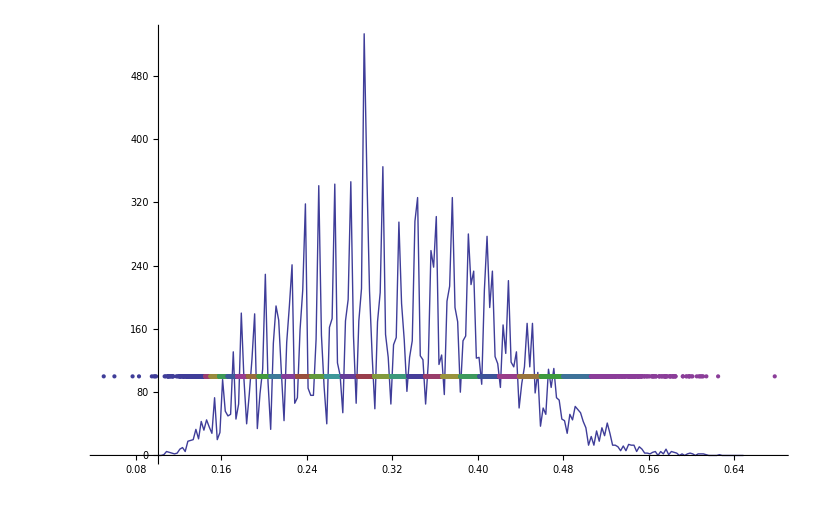

```mathematica
Show[{
ListLinePlot[Hist1D[op⟦All,2⟧,{0.1,0.65},0.0025],PlotRange->All],
ListPlot[TrWith[#⟦All,2⟧,100]&/@sop,PlotRange->All]
}]
```

```mathematica
Clear[bdPeaks]
```

```mathematica
dat=Partition[sop⟦1⟧,IntegerPart[Length[sop⟦1⟧]/3]];
```

```mathematica
FindFit[#,a Exp[-(x-μ)^2/(2 σ^2)],{{a,Length[#]},{μ,Mean[#]},{σ,StandardDeviation[#]}},x]&/@dat
```

dat

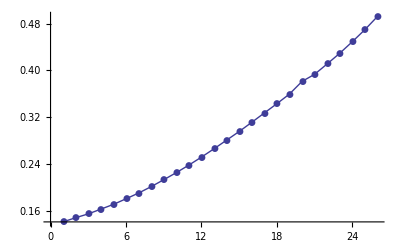

```mathematica
ListLinePlot[(bdPeaks[#,3,0.001]&/@sop)⟦All,1⟧⟦;;-2⟧,PlotMarkers->Automatic]
```

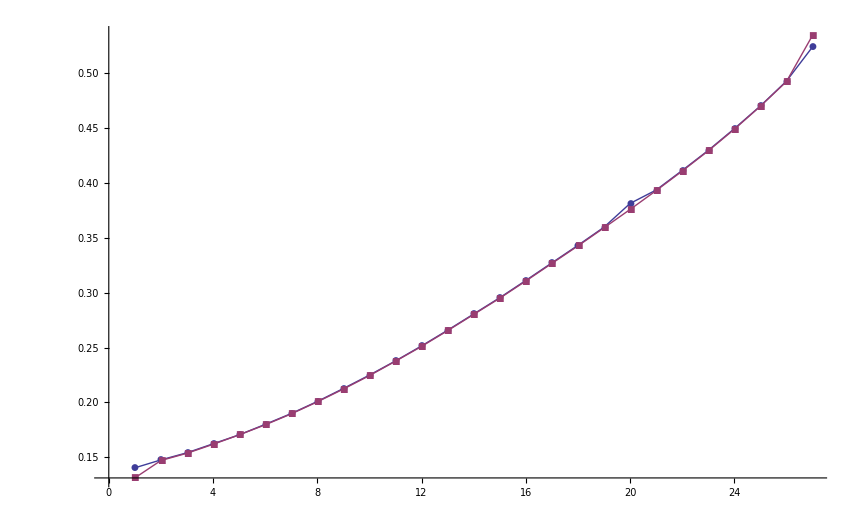

```mathematica
ListLinePlot[{Evaluate[bdPeaks[#,3,0.001]&/@sop]⟦All,1⟧,Evaluate[bdPeaks1[#,3]&/@sop]⟦All,1⟧},PlotMarkers->Automatic]
```

```mathematica
TableForm[Flatten/@Transpose[{bdPeaks[#,3,0.001]&/@sop,nPeaks/@sop,τPeaks[#,3,25,500]&/@sop}]]
```

0.140478 | 0.00497473 | 221 | 1.80189 | 0.179267
0.147706 | 0.000928364 | 90 | 3.10625 | 0.743359
0.154169 | 0.000944485 | 127 | 2.35701 | 0.867511
0.162322 | 0.00117923 | 205 | 1.9791 | 0.492622
0.17047 | 0.000960027 | 246 | 2.29093 | 0.722501
0.180012 | 0.00125422 | 390 | 1.77648 | 0.276265
0.189881 | 0.00119256 | 419 | 1.84158 | 0.44801
0.200854 | 0.00133668 | 513 | 1.69213 | 0.369322
0.212686 | 0.00139657 | 642 | 1.44597 | 0.30158
0.224851 | 0.00147767 | 699 | 1.42648 | 0.345013
0.237787 | 0.00168817 | 863 | 1.22255 | 0.244234
0.251448 | 0.00154535 | 843 | 1.16304 | 0.230261
0.265732 | 0.00181833 | 930 | 0.986765 | 0.175272
0.280512 | 0.00182129 | 981 | 0.867565 | 0.118374
0.295317 | 0.00179552 | 1607 | 0.814413 | 0.111718
0.311036 | 0.00196189 | 1102 | 0.737852 | 0.103762
0.327056 | 0.00227169 | 1036 | 0.646416 | 0.0840706
0.343018 | 0.00223844 | 1143 | 0.597547 | 0.0661295
0.359507 | 0.00225862 | 1206 | 0.524245 | 0.0441378
0.381135 | 0.00317183 | 1241 | 0.516436 | 0.0476479
0.393352 | 0.00266182 | 1257 | 0.474077 | 0.0248535
0.411166 | 0.00270382 | 1240 | 0.445623 | 0.017601
0.429418 | 0.00306366 | 1036 | 0.43121 | 0.0425342
0.449191 | 0.00311588 | 885 | 0.384661 | 0.0121257
0.469869 | 0.00313915 | 617 | 0.399233 | 0.0474848
0.492486 | 0.00386913 | 434 | 0.443482 | 0.064685
0.52361 | 0.00548249 | 393 | 0.547448 | 0.0584042

```mathematica
TableForm[Flatten/@Transpose[{bdPeaks[#,3]&/@sop,nPeaks/@sop,τPeaks[#,3,25,500]&/@sop}]]
```

0.131274 | 0.00681752 | 221 | 1.80189 | 0.179267
0.147144 | 0.000944641 | 90 | 3.10625 | 0.743359
0.15373 | 0.00112051 | 127 | 2.35701 | 0.867511
0.161863 | 0.00124811 | 205 | 1.9791 | 0.492622
0.170459 | 0.00134928 | 246 | 2.29093 | 0.722501
0.179605 | 0.00143678 | 390 | 1.77648 | 0.276265
0.18958 | 0.00142262 | 419 | 1.84158 | 0.44801
0.200513 | 0.00157063 | 513 | 1.69213 | 0.369322
0.212165 | 0.00159191 | 642 | 1.44597 | 0.30158
0.224418 | 0.00176685 | 699 | 1.42648 | 0.345013
0.23752 | 0.00182281 | 863 | 1.22255 | 0.244234
0.251013 | 0.00183083 | 843 | 1.16304 | 0.230261
0.265327 | 0.00206826 | 930 | 0.986765 | 0.175272
0.280124 | 0.00212328 | 981 | 0.867565 | 0.118374
0.294872 | 0.00208711 | 1607 | 0.814413 | 0.111718
0.310541 | 0.00222763 | 1102 | 0.737852 | 0.103762
0.326552 | 0.00245938 | 1036 | 0.646416 | 0.0840706
0.342478 | 0.00240791 | 1143 | 0.597547 | 0.0661295
0.358965 | 0.00248399 | 1206 | 0.524245 | 0.0441378
0.375656 | 0.00259477 | 1241 | 0.516436 | 0.0476479
0.392809 | 0.00283995 | 1257 | 0.474077 | 0.0248535
0.410621 | 0.00290079 | 1240 | 0.445623 | 0.017601
0.429023 | 0.00323484 | 1036 | 0.43121 | 0.0425342
0.448684 | 0.00332202 | 885 | 0.384661 | 0.0121257
0.469665 | 0.00335726 | 617 | 0.399233 | 0.0474848
0.492067 | 0.00414977 | 434 | 0.443482 | 0.064685
0.534089 | 0.0150369 | 393 | 0.547448 | 0.0584042

```mathematica
ττ=Partition[sop⟦2⟧⟦All,3⟧,IntegerPart[Length[sop⟦2⟧]/3]];
```

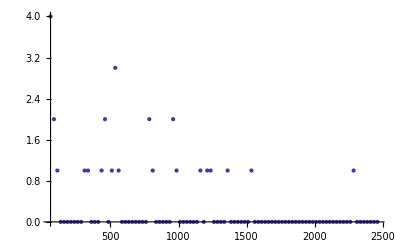

```mathematica
ListPlot[Hist1D[ττ⟦1⟧,{Min[ττ⟦1⟧]-5,Max[ττ⟦1⟧]+5},25],PlotRange->All]
```

```mathematica
hh=Hist1D[#,{Min[#]-2×25,Max[#]+2×25},25]&/@ττ;
```

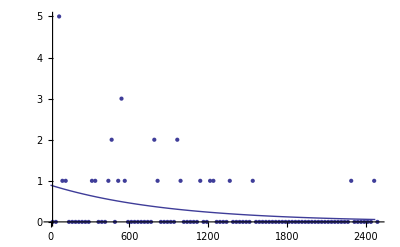
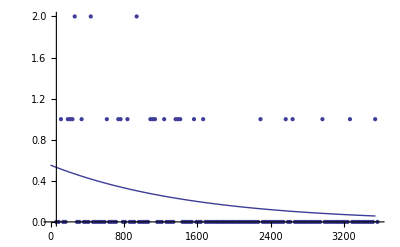
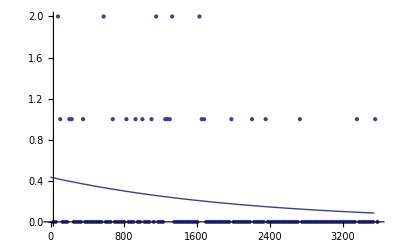

```mathematica
Table[Show[{
ListPlot[hh⟦i⟧,PlotRange->All,PlotStyle->Thick],
Plot[Evaluate[Normal[NonlinearModelFit[hh⟦i⟧,a Exp[-t/τ],{{a,0.5 Max[hh⟦i⟧⟦All,2⟧]},{τ,Mean[ττ⟦i⟧]}},t,MaxIterations->∞]]],{t,0,Max[ττ⟦i⟧]}]
}],{i,Length[hh]}]
```

```mathematica
(#[Table[τ/.FindFit[hh⟦i⟧, a Exp[-t/τ],{{a,Max[ττ⟦i⟧]},{τ,Mean[ττ⟦i⟧]}},t],{i,Length[hh]}]]&/@{Mean,StandardError})0.002
```

{1.42954,0.342479}

### Julianne’s Data

```mathematica
datpathJ="/Users/balijepalliak/Research/Experiments/PEGModelData/JuliannesData/";
```

```mathematica
Select[ReadPyEventMeta[datpathJ<>"/7-6&7-2010_4M/50mV/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&]//Length
```

204345

```mathematica
d=ReadPyEventMeta[datpathJ<>"/7-6&7-2010_4M/50mV/eventMD.tsv"];//AbsoluteTiming
```

{41.49841,Null}

```mathematica
dd=Select[d, #⟦6⟧⟦1⟧≠-1&];
```

```mathematica
d1=dd⟦All,6⟧⟦All,1⟧;//AbsoluteTiming
```

{0.02993,Null}

```mathematica
h1=PDF1D[d1,{0.1,0.4},0.00075];//AbsoluteTiming
```

{0.27149,Null}

```mathematica
Export[HomeDirectory[]<>"/Desktop/hist.csv",Transpose[PadRight[h1⟦All,2⟧,717,0]]]
```

/Users/balijepalliak/Desktop/hist.csv

```mathematica
Export[datpathJ<>"/7-6&7-2010_4M/50mV/bd_restime.tsv",Transpose[{dd⟦All,6⟧⟦All,1⟧,dd⟦All,2⟧⟦All,1⟧,dd⟦All,7⟧⟦All,1⟧,ConstantArray[0,Length[dd]]}],"TSV"]
```

/Users/balijepalliak/Research/Experiments/PEGModelData/JuliannesData//7-6&7-2010_4M/50mV/bd_restime.tsv

```mathematica
Export[datpathJ<>"/7-6&7-2010_4M/50mV/bd_hist.tsv",h1,"TSV"]
```

/Users/balijepalliak/Research/Experiments/PEGModelData/JuliannesData//7-6&7-2010_4M/50mV/bd_hist.tsv

```mathematica
First/@FindClusters[c1⟦2⟧,10,Method->"Optimize"]
```

{{0.152875,568},{0.162625,685},{0.172375,710},{0.173125,774},{0.174625,863},{0.185125,981},{0.187375,895},{0.194125,843},{0.197125,1043},{0.208375,1089}}

```mathematica
c2=FindClusters[Sort[d1]];//AbsoluteTiming
```

```mathematica
c2=FindClusters[d1⟦;;50000⟧,10];//AbsoluteTiming
```

{5.279659,Null}

```mathematica
Length/@{c2,d1⟦;;50000⟧}
```

{50000,50000}

```mathematica
Sort[Transpose[{d1⟦;;50000⟧,c2}],#1⟦1⟧<#2⟦1⟧&]
```

{{0.01326,8},{0.0189,8},{0.01912,8},{0.01923,8},{0.01934,8},{0.01945,8},{0.01945,8},{0.01947,8},{0.01948,8},{0.02249,8},{0.02322,8},{0.02325,8},{0.0236,8},{0.0241,8},{0.02501,8},{0.02606,8},{0.02635,8},{0.02648,8},{0.02831,8},{0.02867,8},{0.02907,8},{0.02916,8},{0.02924,8},{0.02929,8},{0.02941,8},«49950»,{0.89997,9},{0.90057,9},{0.90155,9},{0.90163,9},{0.90204,9},{0.90316,9},{0.90407,9},{0.90487,9},{0.90499,9},{0.90716,9},{0.90758,9},{0.90825,9},{0.91117,9},{0.91283,9},{0.91429,9},{0.91659,9},{0.91676,9},{0.92426,9},{0.92481,9},{0.9299,9},{0.95562,9},{2.79414,9},{4.2447,9},{5.1462,9},{5.28384,9}}

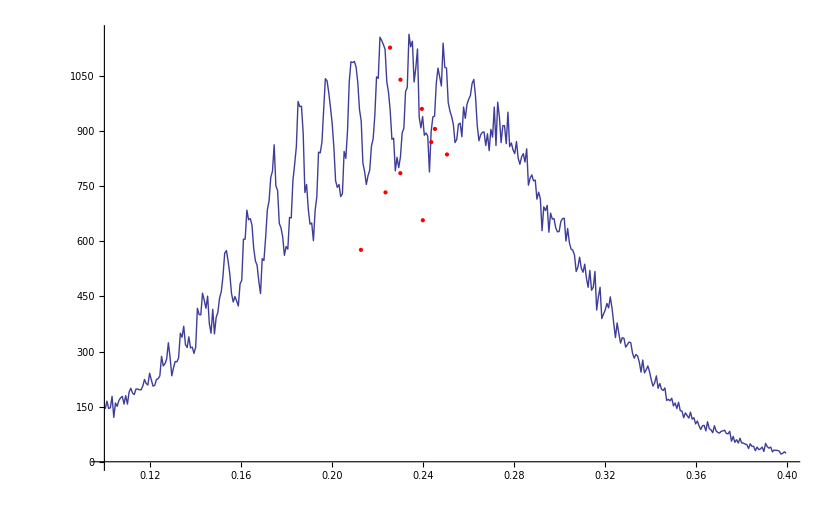

```mathematica
Show[{
ListLinePlot[h1],
ListPlot[Mean/@FindClusters[c1⟦2⟧,10,DistanceMethod->Method->"Optimize"],PlotStyle->Red]
}]
```

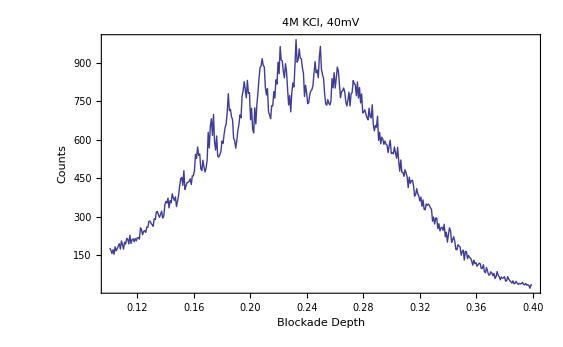

```mathematica
MergePlotPEGBlockade[(datpathJ<>"7-6&7-2010_4M/40mV/"<>#)&/@{"40mV001","40mV002","40mV003","40mV004"},"4M KCl, 40mV",{0.1,0.4},0.00075]
```

```mathematica
d=ReadPyEventMeta[datpathJ<>"/7-14-2010_3.5M/20mV/eventMD.tsv"];//AbsoluteTiming
```

{10.30092,Null}

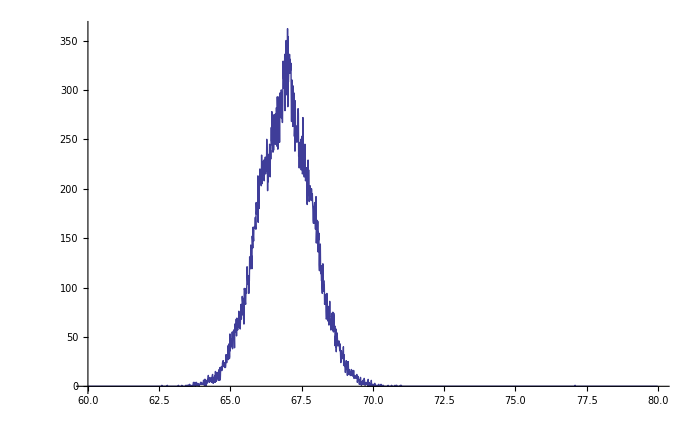

```mathematica
ListLinePlot[Hist1D[Select[d⟦All,2⟧⟦All,1⟧,#≠-1&],{60, 80},0.01],PlotRange->All]
```

```mathematica
Select[ReadPyEventMeta[datpathJ<>"/7-14-2010_3.5M/20mV/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&]//Length
```

192497

```mathematica
Select[ReadPyEventMeta[datpathJ<>"/7-14-2010_3.5M/50mVGain50/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&]//Length
```

135903

```mathematica
,datpathJ<>"/7-14-2010_3.5M/50mVGain50"
```

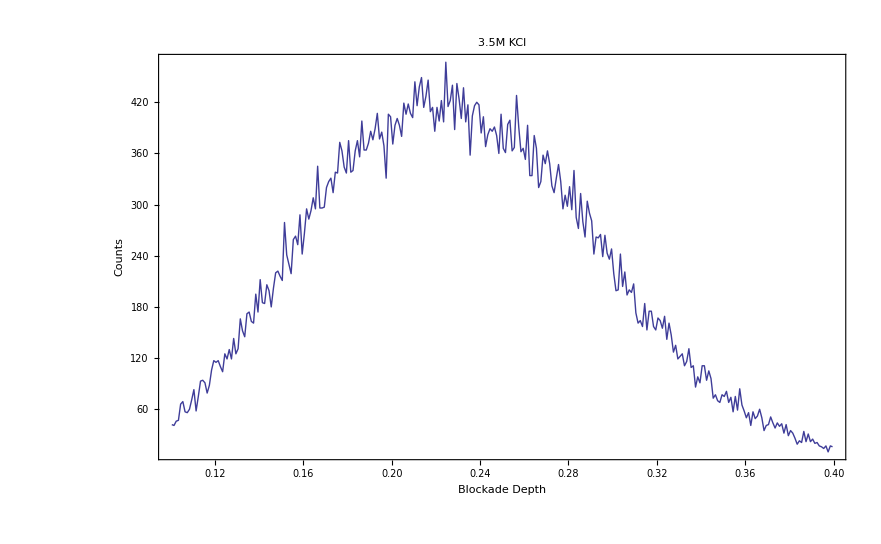

```mathematica
PlotPEGBlockade[{datpathJ<>"/7-14-2010_3.5M/20mV"},"3.5M KCl",{0.1,0.4},0.001]
```

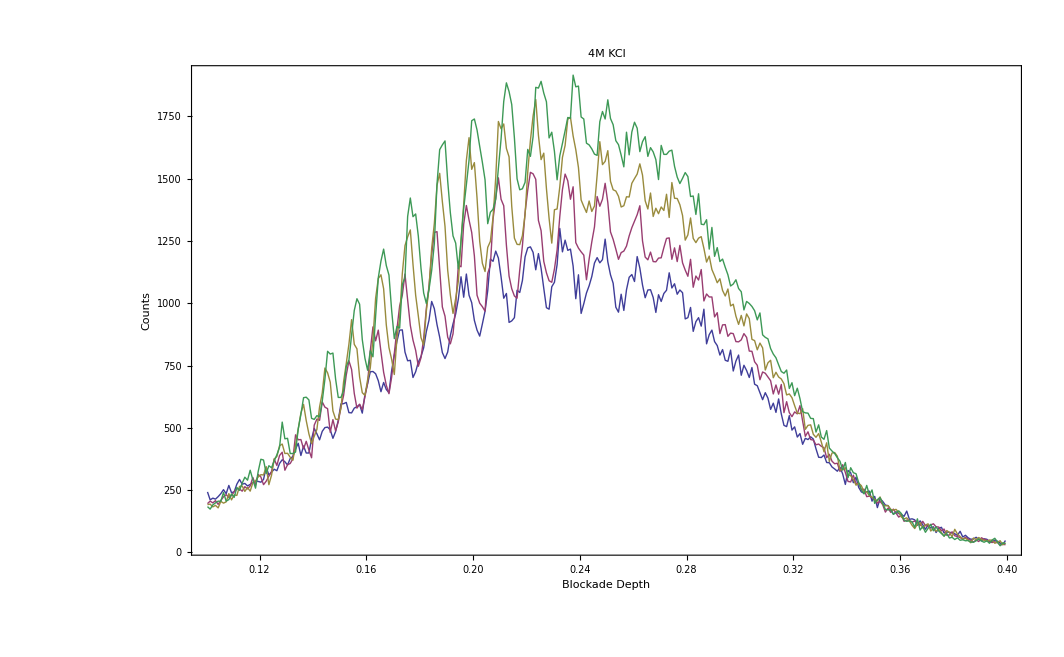

```mathematica
Show[{
PlotPEGBlockade[{datpathJ<>"/7-6&7-2010_4M/40mV",datpathJ<>"/7-6&7-2010_4M/50mV",datpathJ<>"/7-6&7-2010_4M/60mV",datpathJ<>"/7-6&7-2010_4M/70mV"},"4M KCl",{0.1,0.4},0.001]
}]
```

```mathematica
goldpath="/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/Take2LongerDataPNAS"
```

/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/Take2LongerDataPNAS

```mathematica
pydispevent[ReadEventDat[goldpath<>"/eventTS.csv"],ReadPyEventMeta[goldpath<>"/eventMD.tsv"],{100,30}]
```

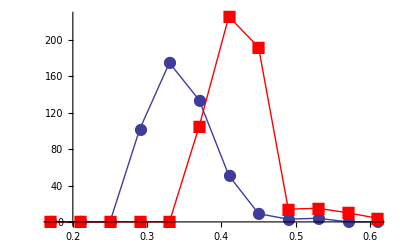

```mathematica
ListLinePlot[{
Hist1D[Select[ReadPyEventMeta[goldpath<>"/eventMD_low.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.15,0.65},0.04],
Hist1D[Select[ReadPyEventMeta[goldpath<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.15,0.65},0.04]
},PlotRange->All,PlotMarkers->{Automatic,16},PlotStyle->{Thick,{Red,Thick}}]
```

```mathematica
Block[{ts=ReadEventDat["/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/SteadyStateHeating/20120725/21Cr1M40mV/eventTS.csv"], md=ReadEventMeta["/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/SteadyStateHeating/20120725/21Cr1M40mV/eventMD.tsv"]},
Manipulate[DisplayEvent[ts⟦i⟧,md⟦i⟧],{i,1,Length[ts],1}]
]
```

```mathematica
evnt⟦48⟧⟦;;5⟧
```

{-84.9027,-113.895,501,512,-102.786}

```mathematica
Manipulate[DisplayEvent[evnt⟦i⟧],{i,1,Length[evnt],1}]
```

```mathematica
{MovingAverage[Abs[evnt⟦8⟧⟦5;;evnt⟦8⟧⟦3⟧-50⟧],100]//Mean,MovingAverage[Abs[evnt⟦8⟧⟦evnt⟦8⟧⟦4⟧+55;;⟧],100]//Mean}
```

{113.143,113.841}

```mathematica
{MovingAverage[Abs[evnt⟦8⟧⟦5;;evnt⟦8⟧⟦3⟧-50⟧],100]//Mean,MovingAverage[Abs[evnt⟦8⟧⟦evnt⟦8⟧⟦4⟧+55;;⟧],100]//Mean}//Mean
```

113.492

```mathematica
DSolve[t''[x]+q/κ==0,t,x]
```

{{t→Function[{x},-(q x^2)/(2 κ)+C[1]+x C[2]]}}

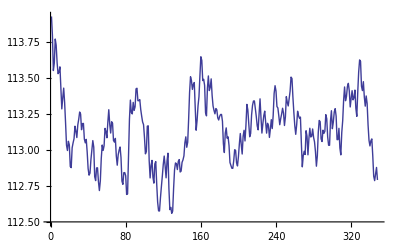

```mathematica
ListLinePlot[MovingAverage[Abs[evnt⟦8⟧⟦5;;evnt⟦8⟧⟦3⟧-50⟧],100]]
```

```mathematica
evnt⟦8⟧⟦4⟧
```

1091

```mathematica
evnt⟦8⟧⟦5;;⟧
```

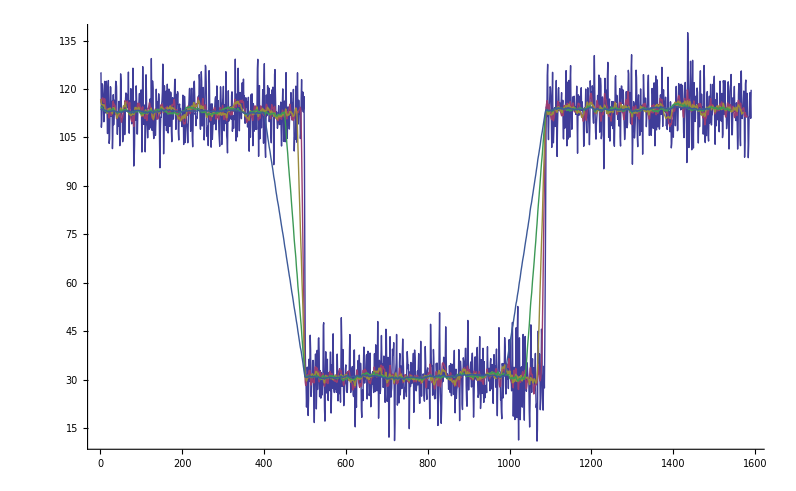

```mathematica
ListLinePlot[MovingAverage[Abs[evnt⟦8⟧⟦5;;⟧],#]&/@{1,10,20,50,100},PlotRange->All]
```

```mathematica
DSolve[{D[f[t], t]==k c (1-f[t]/fmax)- kd f[t]},f[t],t]
```

{{f[t]→(c ⅇ^(((-c k-fmax kd) t)/fmax+((c k+fmax kd) t)/fmax) fmax k)/(c k+fmax kd)+ⅇ^(((-c k-fmax kd) t)/fmax) C[1]}}

### Comparing Data From Different Channels

```mathematica
rootpath=NotebookDirectory[]<>"../../PEGModelData/ArvindsData/PEGMixture/3M_20121219/analysis/";
```

```mathematica
Δio[i1path_,i2path_]:=Mean[Import[i2path,"TSV"]⟦All,2⟧]-Mean[Import[i1path,"TSV"]⟦All,2⟧]
```

#### 40 mV

```mathematica
dio=Δio[rootpath<>"/m40mV12 i_io_open_width io2",rootpath<>"m40mV13 i_io_open_width and SD io1"]
```

2.34311

```mathematica
Length/@{Import[rootpath<>"/m40mV12 i_io_open_width io2","TSV"],Import[rootpath<>"m40mV13 i_io_open_width and SD io1","TSV"]}
```

{18078,17769}

```mathematica
Export[rootpath<>"m40mV12_13 i_io_open_width io2",Flatten[{Import[rootpath<>"/m40mV12 i_io_open_width io2","TSV"],{(#⟦1⟧#⟦2⟧-dio)/(#⟦2⟧-dio),#⟦2⟧-dio,#⟦3⟧}&/@Import[rootpath<>"m40mV13 i_io_open_width and SD io1","TSV"]},1],"TSV"]
```

/Users/balijepalliak/Research/Experiments/AnalysisTools/pyEventAnalysis/../../PEGModelData/ArvindsData/PEGMixture/3M_20121219/analysis/m40mV12_13 i_io_open_width io2

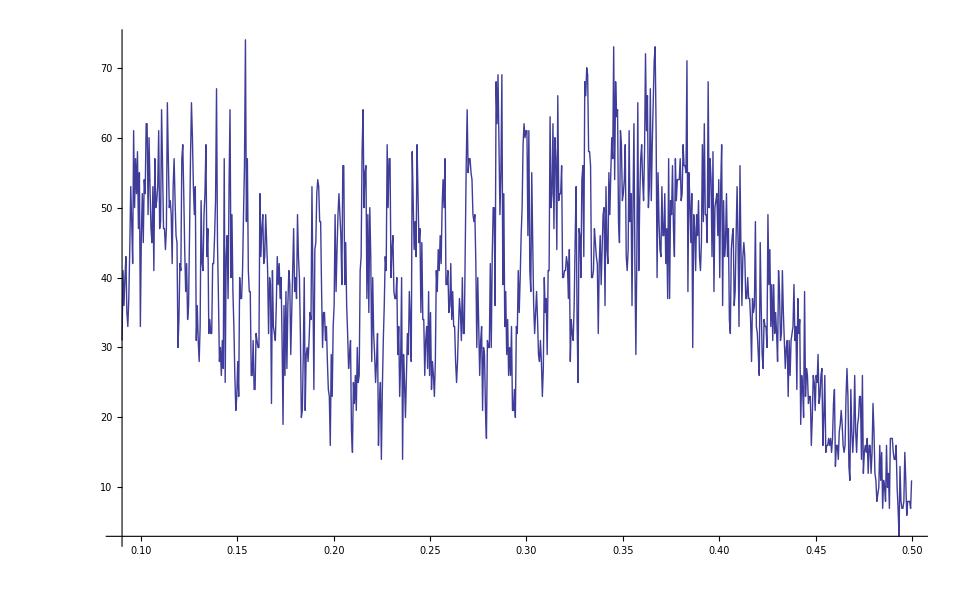

```mathematica
ListLinePlot[Hist1D[Flatten[{Import[rootpath<>"/m40mV12 i_io_open_width io2","TSV"]⟦All,1⟧,(#⟦1⟧#⟦2⟧+0.8dio)/(#⟦2⟧+0.8dio)&/@Import[rootpath<>"m40mV13 i_io_open_width and SD io1","TSV"]}],{0.09,0.5},0.0005],PlotRange->All]
```

```mathematica
Manipulate[ListLinePlot[{
PDF1D[Import[rootpath<>"/m40mV12 i_io_open_width io2","TSV"]⟦All,1⟧,{0.09,0.5},0.001],
PDF1D[(#⟦1⟧#⟦2⟧+k dio)/(#⟦2⟧+k dio)&/@Import[rootpath<>"m40mV13 i_io_open_width and SD io1","TSV"],{0.09,0.5},0.001]
},PlotRange->All],{{k,1},-2,2}]
```

#### 60 mV

```mathematica
dio60=-Δio[rootpath<>"/m60mV12 i_io_open_width and SD io1",rootpath<>"m60mV12 i_io_open_width io2"]
```

1.90865

```mathematica
Length/@{Import[rootpath<>"/m60mV12 i_io_open_width and SD io1","TSV"],Import[rootpath<>"m60mV12 i_io_open_width io2","TSV"]}
```

{13222,17068}

```mathematica
Export[rootpath<>"m40mV12_13 i_io_open_width io2",Flatten[{Import[rootpath<>"/m40mV12 i_io_open_width io2","TSV"],{(#⟦1⟧#⟦2⟧-dio60)/(#⟦2⟧-dio60),#⟦2⟧-dio,#⟦3⟧}&/@Import[rootpath<>"m40mV13 i_io_open_width and SD io1","TSV"]},1],"TSV"]
```

/Users/balijepalliak/Research/Experiments/AnalysisTools/pyEventAnalysis/../../PEGModelData/ArvindsData/PEGMixture/3M_20121219/analysis/m40mV12_13 i_io_open_width io2

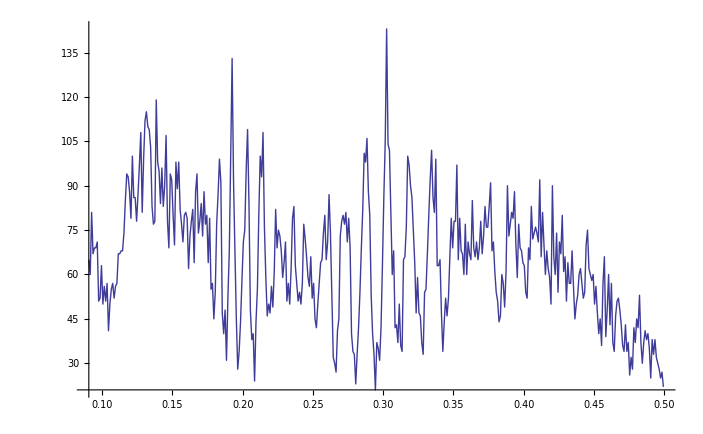

```mathematica
ListLinePlot[Hist1D[Flatten[{Import[rootpath<>"/m60mV12 i_io_open_width and SD io1","TSV"]⟦All,1⟧,(#⟦1⟧#⟦2⟧-2.5dio60)/(#⟦2⟧-2.5dio60)&/@Import[rootpath<>"m60mV12 i_io_open_width io2","TSV"]}],{0.09,0.5},0.001],PlotRange->All]
```

```mathematica
Manipulate[ListLinePlot[{
PDF1D[Import[rootpath<>"/m60mV12 i_io_open_width and SD io1","TSV"]⟦All,1⟧,{0.09,0.5},0.001],
PDF1D[(#⟦1⟧#⟦2⟧-k dio60)/(#⟦2⟧-k dio60)&/@Import[rootpath<>"m60mV12 i_io_open_width io2","TSV"],{0.09,0.5},0.001]
},PlotRange->All],{{k,2},-3,3}]
```

```mathematica
GraphicsColumn[ListLinePlot[#,PlotRange->All]&/@{PDF1D[Import[rootpath<>"/m60mV12 i_io_open_width and SD io1","TSV"]⟦All,1⟧,{0.09,0.5},0.001],
PDF1D[(#⟦1⟧#⟦2⟧- 2.1dio60)/(#⟦2⟧-2.1dio60)&/@Import[rootpath<>"m60mV12 i_io_open_width io2","TSV"],{0.09,0.5},0.001]}]
```

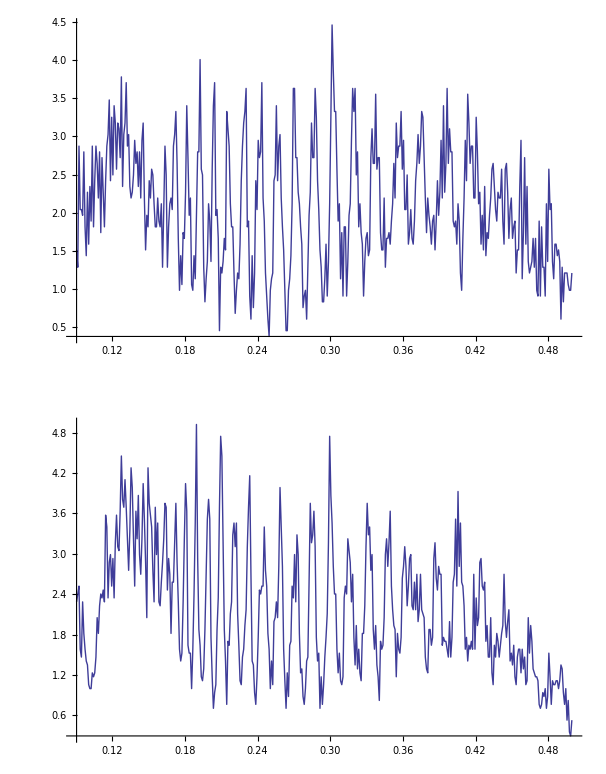

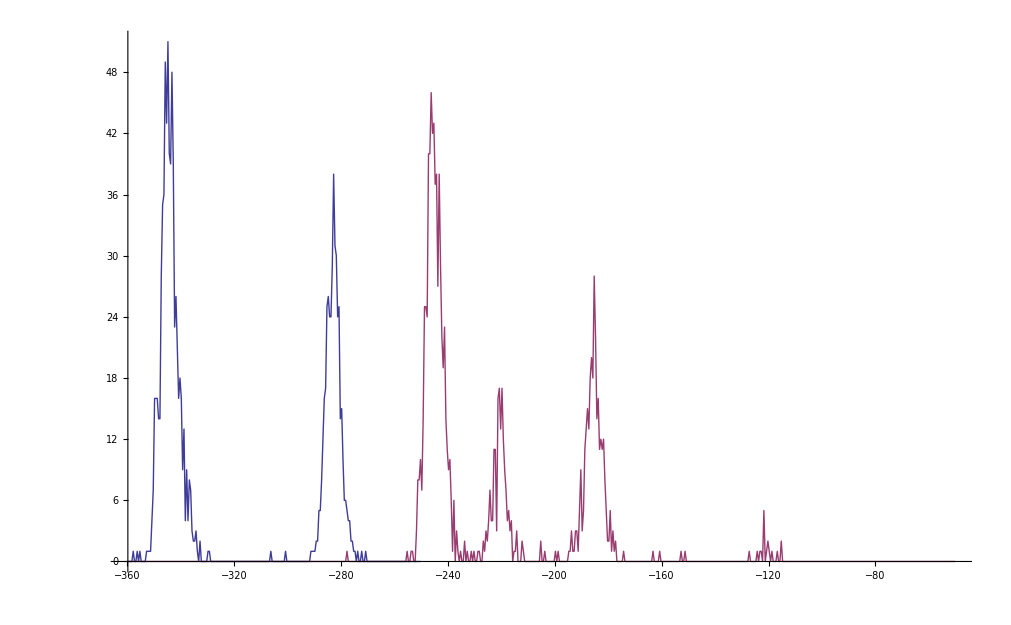

```mathematica
ListLinePlot[{
Hist1D[Select[ReadPyEventMeta["/Users/balijepalliak/Google Drive/eventMD.tsv"]⟦All,2⟧⟦All,1⟧,#≠-1&],{-360,-250},0.5],
Hist1D[Select[ReadPyEventMeta["/Users/balijepalliak/Google Drive/eventMD.tsv"]⟦All,3⟧⟦All,1⟧,#≠-1&],{-360,-50},0.5]
},PlotRange->All]
```

```mathematica
Select[ReadPyEventMeta["/Users/balijepalliak/Google Drive/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&]//Length
```

378

```mathematica
100/(1-0.26)
```

135.135

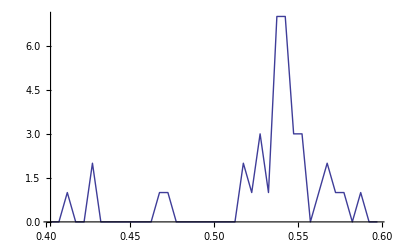

```mathematica
ListLinePlot[{
Hist1D[Select[ReadPyEventMeta["/Users/balijepalliak/Google Drive/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.4,0.6},0.005]
},PlotRange->All]
```

### EBS AC Rig 4M KCl: 07 Jan 2013: py code

```mathematica
tt=ReadPyEventMeta["/Users/balijepalliak/Research/Experiments/PEGModelData/ArvindsData/PEGMixture/4M_20130107/m60mV5/eventMD.tsv"];
```

```mathematica
#[Select[tt⟦All,2⟧⟦All,1⟧,#≠-1&]]&/@{Mean,StandardDeviation,Length}
```

{-212.358,19.3321,20828}

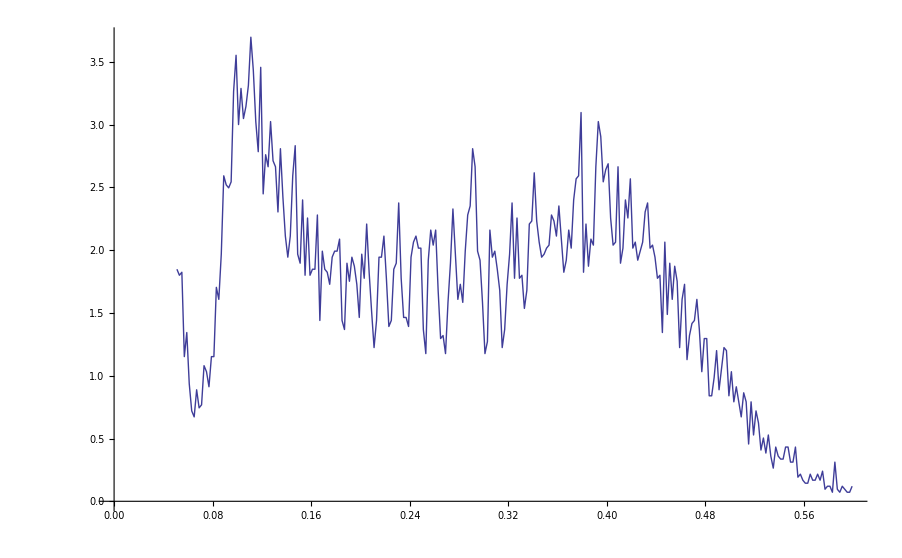

```mathematica
ListLinePlot[PDF1D[Select[tt⟦All,6⟧⟦All,1⟧,#≠-1&],{0.05,0.6},0.002]]
```